```mathematica
Experiments with the Chua's Circuit

(*
==Chua's circuit==
the double-scroll attractor (sometimes known as Chua's attractor) is a strange attractor observed from a physical electronic chaotic circuit (generally,Chua's circuit) with a single nonlinear resistor (see Chua's Diode).The double-scroll system is often described by a system of three nonlinear ordinary differential equations and a 3-segment piecewise-linear equation (see Chua's equations).This makes the system easily simulated numerically and easily manifested physically due to Chua's circuits' simple design.
-http://www.chuacircuits.com/
-https://en.wikipedia.org/wiki/Multiscroll_attractor
dx/dt=c1*(y-x-f(x)) // m0: slope in outer region
   dy/dt=c2*(x-y+z)    // m1: slope in inner region
   dz/dt=-c3*y         // b: Breakpoints
   f(x)=m1*x+(m0-m1)/2*(|x+1|-|x-1|)
*)
```

-Graphics3D-

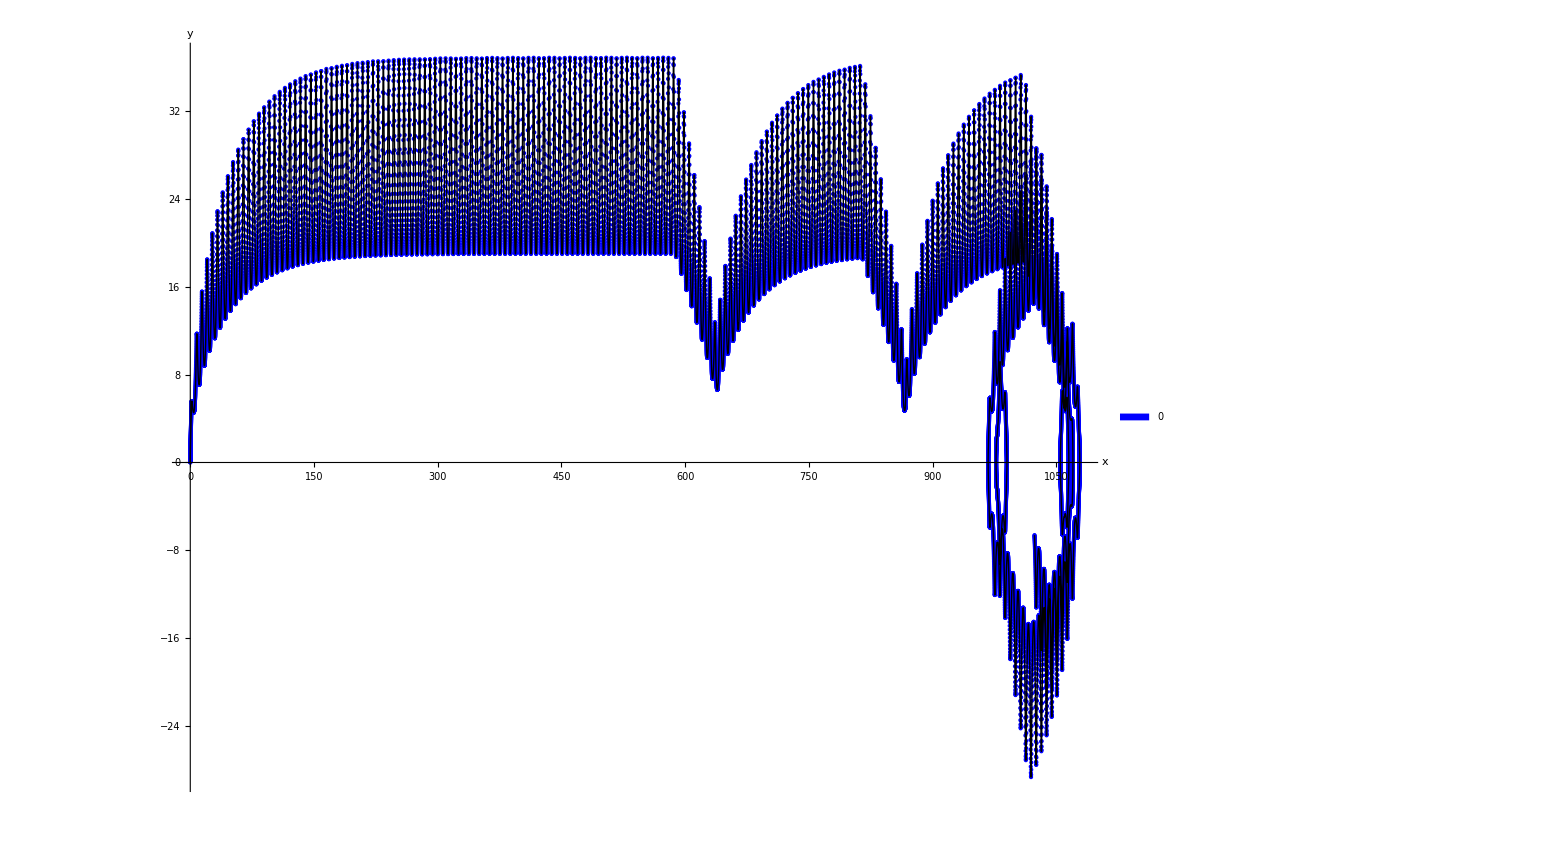

```mathematica
(*ModelLeg, Gravity: 0g, (x),(y), z => JointTorque, friction 0 0, torque 0.00007, damping 0*)
SetDirectory[NotebookDirectory[]];
chaoticController = Import["log0xa5c9f60PitchChaoticController-(x)(y)z-0g-force-0-00007-damping-0.tsv","Data"];
jointMovement = Import["log0xa5c9f60PitchJointModel-(x)(y)z-0g-force-0-00007-damping-0.tsv","Data"];
chaoticControllerTitle= chaoticController[[1,All]];
chaoticController = Drop[chaoticController,1];

jointMovementTitle= jointMovement[[1,All]];
jointMovement = Drop[jointMovement,1][[All,1;;2]];

Show[ListPointPlot3D[{chaoticController}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chaoticControllerTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chaoticController}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}] 

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

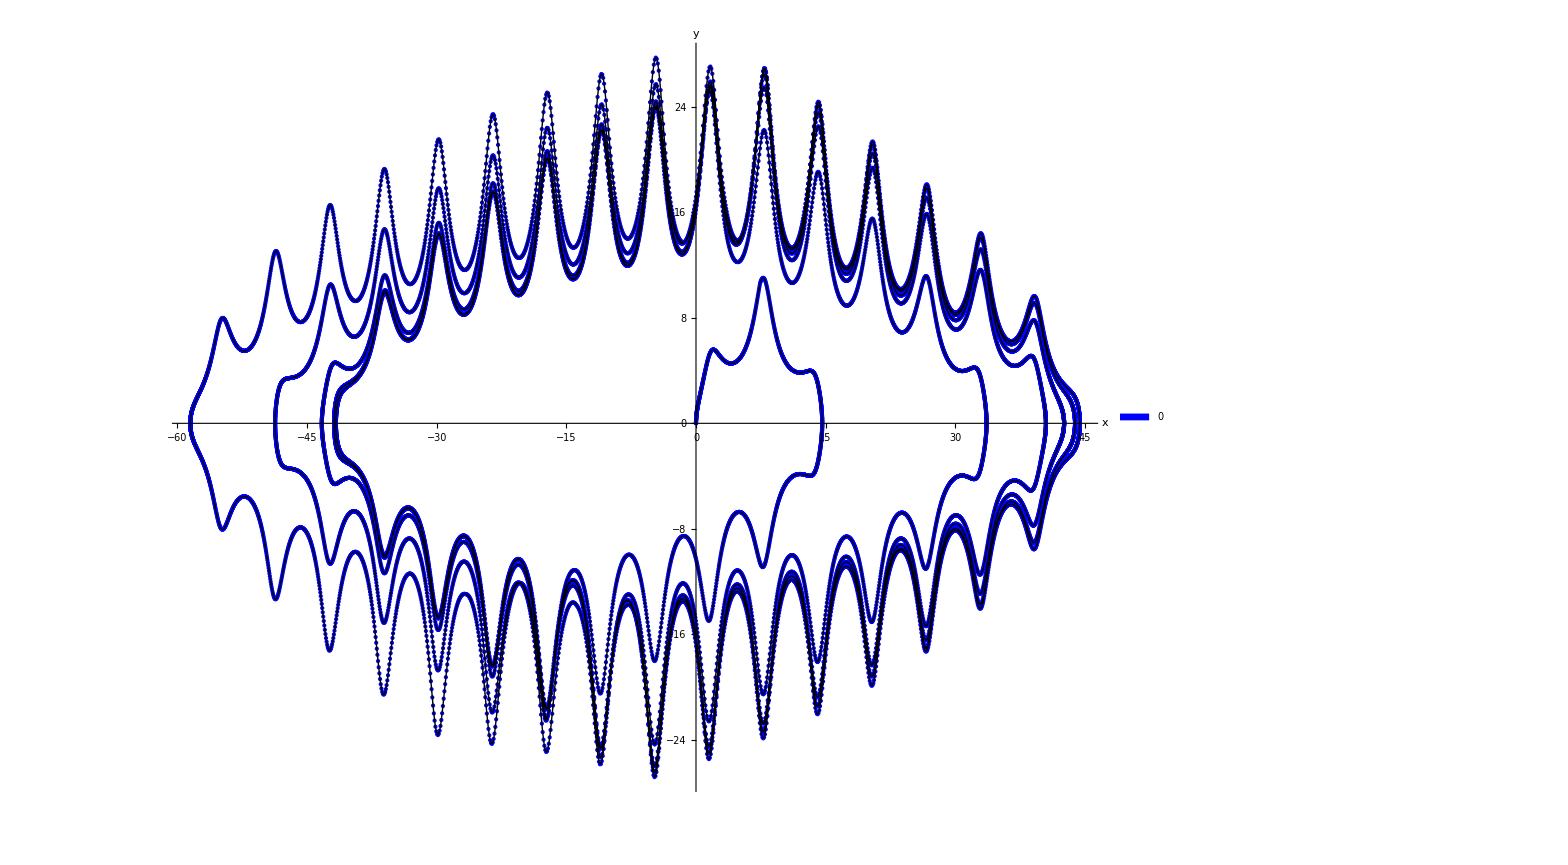

```mathematica
(*ModelLeg, Gravity: 0g, JointPosition => x,(y), z => JointTorque, friction 0 0, torque 0.00007, damping 0*)
SetDirectory[NotebookDirectory[]];
chaoticController = Import["log0xe6069c0PitchChaoticController-px(y)z-0g-force-0-00007-damping-0.tsv","Data"];
jointMovement = Import["log0xe6069c0PitchJointModel-px(y)z-0g-force-0-00007-damping-0.tsv","Data"];
chaoticControllerTitle= chaoticController[[1,All]];
chaoticController = Drop[chaoticController,1];

jointMovementTitle= jointMovement[[1,All]];
jointMovement = Drop[jointMovement,1][[All,1;;2]];

Show[ListPointPlot3D[{chaoticController}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chaoticControllerTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chaoticController}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}] 

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

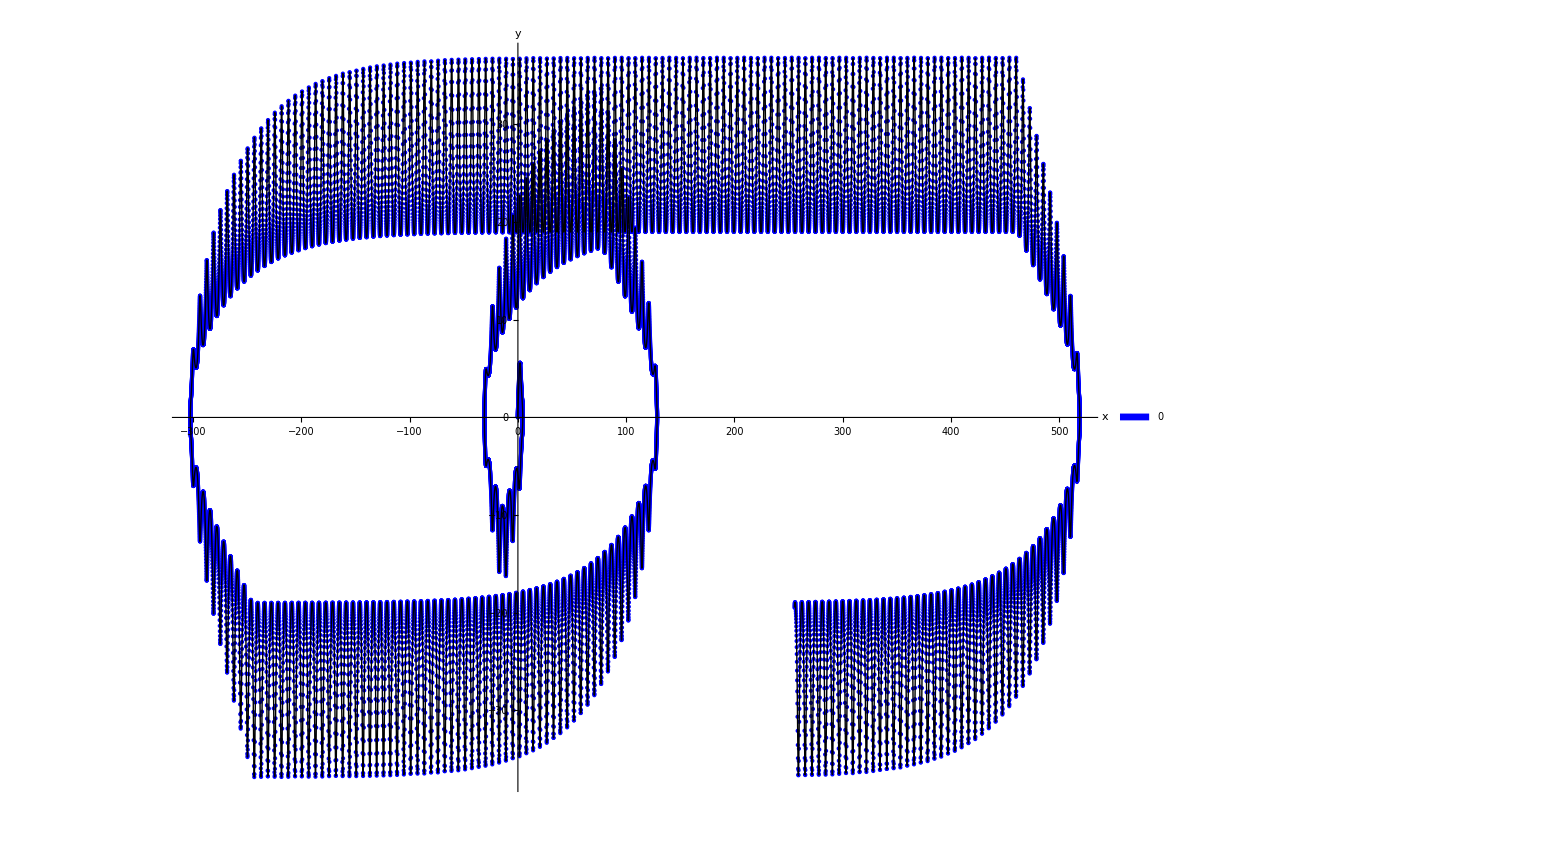

```mathematica
(*ModelLeg, Gravity: 0g, (x),JointPosition => y, z => JointTorque, friction 0 0, torque 0.00007, damping 0*)
SetDirectory[NotebookDirectory[]];
chaoticController = Import["log0xe5fdcd0PitchChaoticController-(x)pyz-0g-force-0-00007-damping-0.tsv","Data"];
jointMovement = Import["log0xe5fdcd0PitchJointModel-(x)pyz-0g-force-0-00007-damping-0.tsv","Data"];
chaoticControllerTitle= chaoticController[[1,All]];
chaoticController = Drop[chaoticController,1];

jointMovementTitle= jointMovement[[1,All]];
jointMovement = Drop[jointMovement,1][[All,1;;2]];

Show[ListPointPlot3D[{chaoticController}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chaoticControllerTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chaoticController}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}] 

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

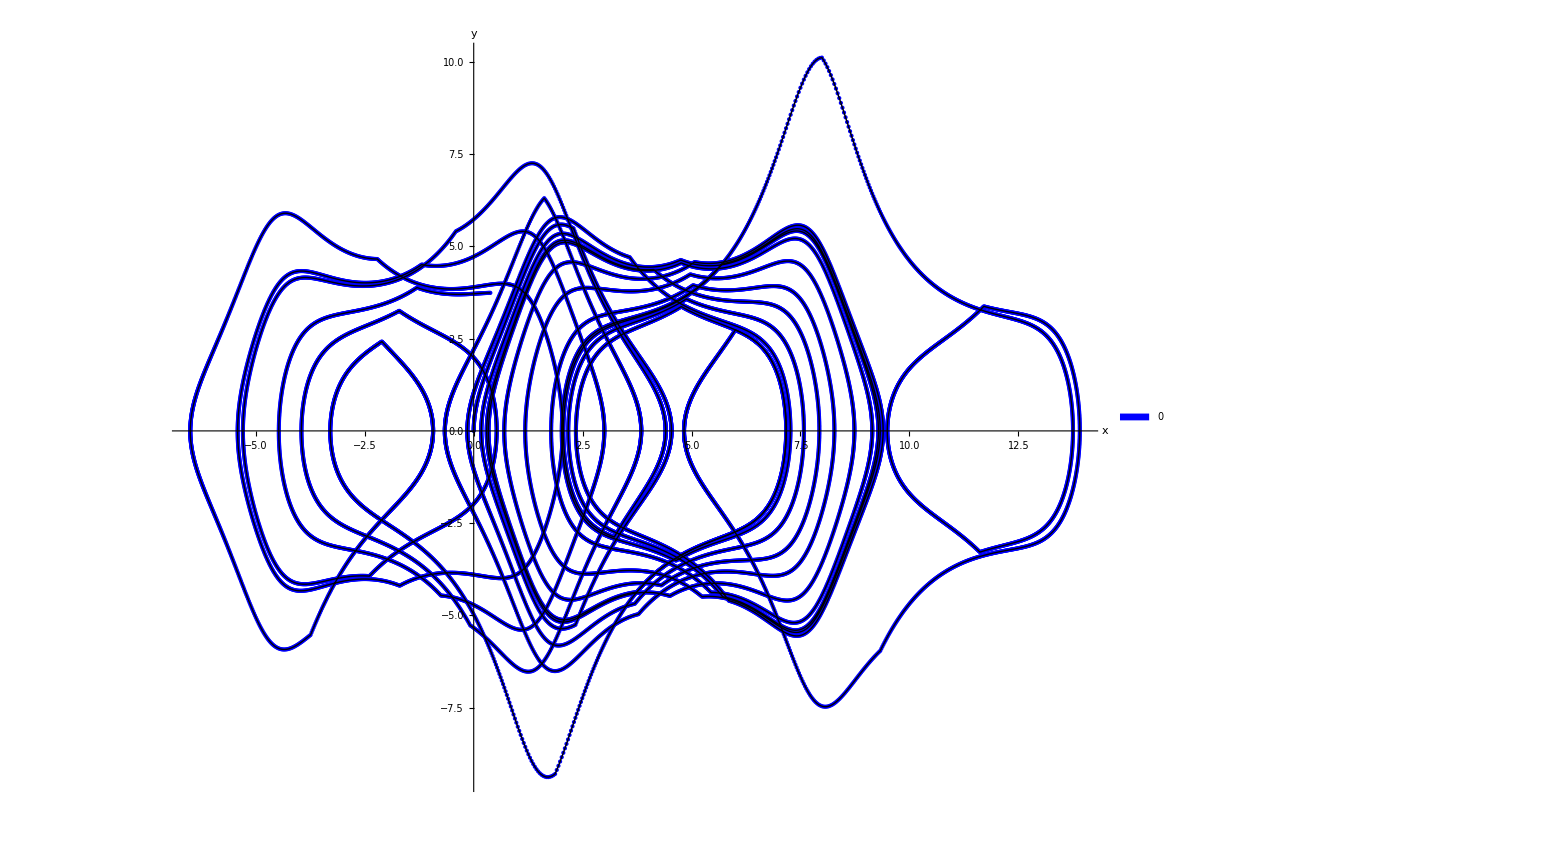

```mathematica
(*ModelLeg, Gravity: 0g, (x),JointPosition => y, z => JointTorque, friction 0 0, torque 0.00007, damping 0*)
SetDirectory[NotebookDirectory[]];
chaoticController = Import["log0x112da070PitchChaoticController.tsv","Data"];
jointMovement = Import["log0x112da070PitchJointModel.tsv","Data"];
chaoticControllerTitle= chaoticController[[1,All]];
chaoticController = Drop[chaoticController,1];

jointMovementTitle= jointMovement[[1,All]];
jointMovement = Drop[jointMovement,1][[All,1;;2]];

Show[ListPointPlot3D[{chaoticController}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chaoticControllerTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chaoticController}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}] 

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

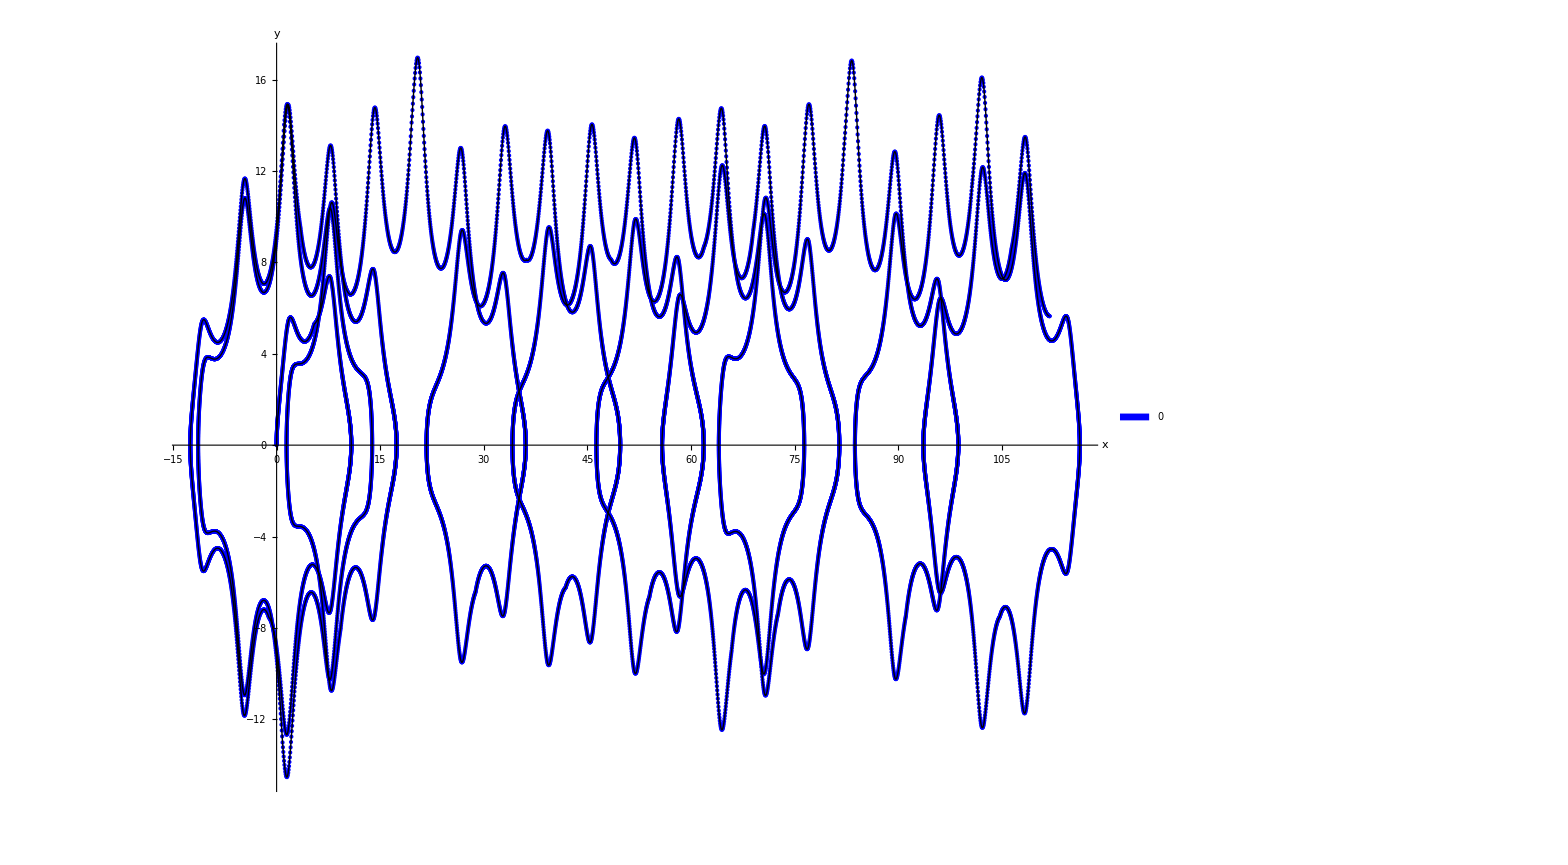

```mathematica
(*ModelLeg, Gravity: 0g, JointVelocity =>x,(y), z => JointTorque, friction 0 0, torque 0.00007, damping 0*)
SetDirectory[NotebookDirectory[]];
chaoticController = Import["log0xe144dc0PitchChaoticController-vx(y)z-0g-force-0-00007-damping-0.tsv","Data"];
jointMovement = Import["log0xe144dc0PitchJointModel-vx(y)z-0g-force-0-00007-damping-0.tsv","Data"];
chaoticControllerTitle= chaoticController[[1,All]];
chaoticController = Drop[chaoticController,1];

jointMovementTitle= jointMovement[[1,All]];
jointMovement = Drop[jointMovement,1][[All,1;;2]];

Show[ListPointPlot3D[{chaoticController}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chaoticControllerTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chaoticController}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}] 

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

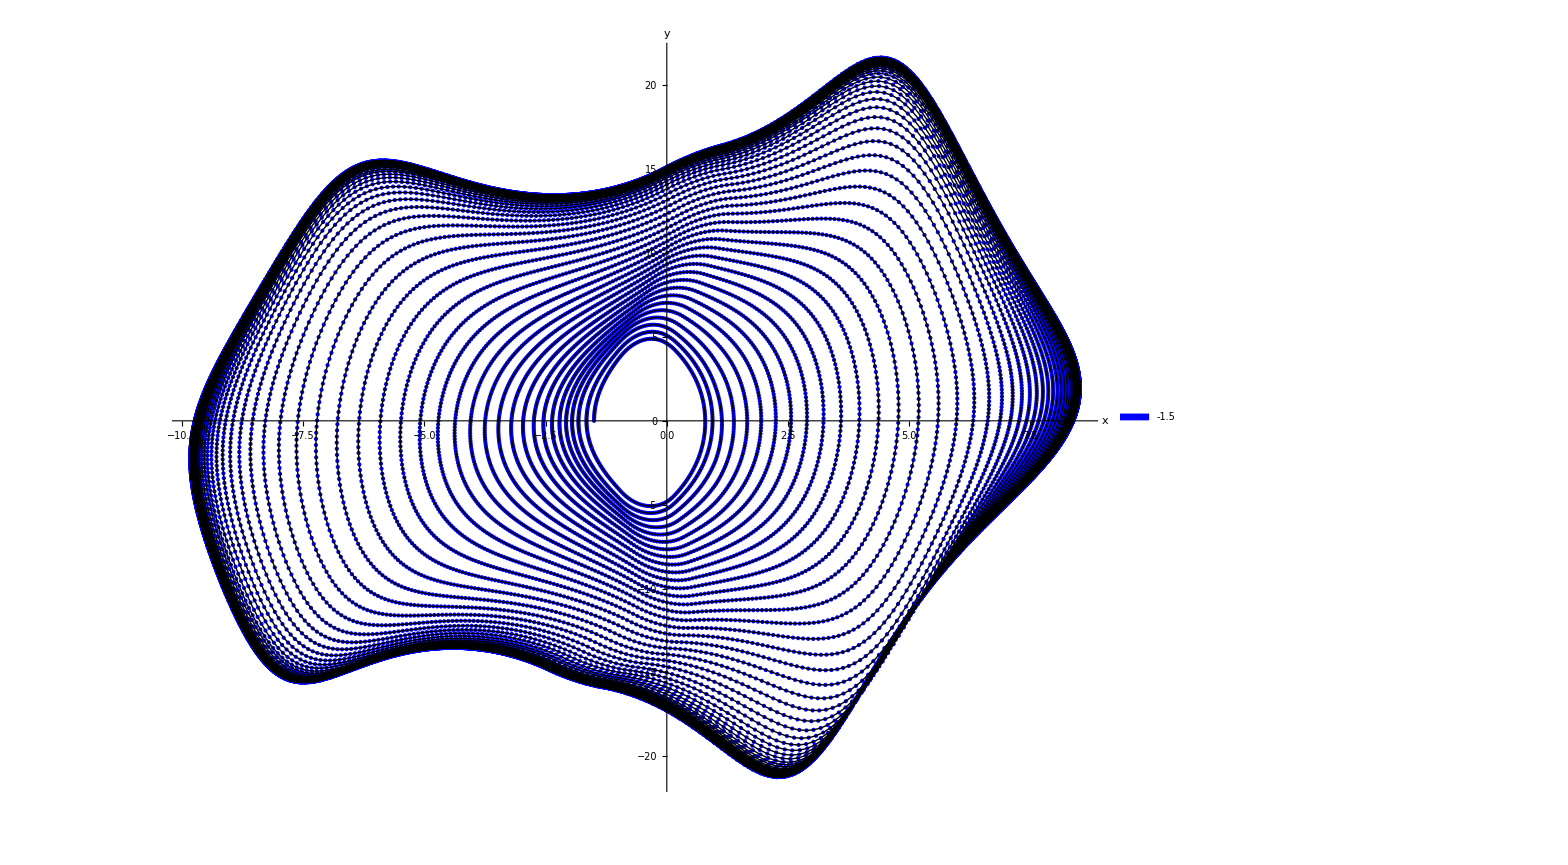

```mathematica
(*ModelLeg, Gravity: 0g, (x),JointVelocity=> y, z => JointTorque, friction 0 0, torque 0.00007, damping 0*)
SetDirectory[NotebookDirectory[]];
chaoticController = Import["log0x11296050PitchChaoticController-(x)vyz-0g-force-0-00007-damping-0.tsv","Data"];
jointMovement = Import["log0x11296050PitchJointModel-(x)vyz-0g-force-0-00007-damping-0.tsv","Data"];
chaoticControllerTitle= chaoticController[[1,All]];
chaoticController = Drop[chaoticController,1];

jointMovementTitle= jointMovement[[1,All]];
jointMovement = Drop[jointMovement,1][[All,1;;2]];

Show[ListPointPlot3D[{chaoticController}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chaoticControllerTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chaoticController}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}] 

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

```mathematica
(*ModelLeg, Gravity: 0g, JointPosition=>x, JointVelocity=>y, z => JointTorque, friction 0 0, torque 0.00007, damping 0*)
SetDirectory[NotebookDirectory[]];
chaoticController = Import["log0xf4e9e40PitchChaoticController-vxpyz-0g-force-0-00007-damping-0.tsv","Data"];
jointMovement = Import["log0xf4e9e40PitchJointModel-vxpyz-0g-force-0-00007-damping-0.tsv","Data"];
chaoticControllerTitle= chaoticController[[1,All]];
chaoticController = Drop[chaoticController,1];

jointMovementTitle= jointMovement[[1,All]];
jointMovement = Drop[jointMovement,1][[All,1;;2]];

Show[ListPointPlot3D[{chaoticController}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chaoticControllerTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chaoticController}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}] 

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

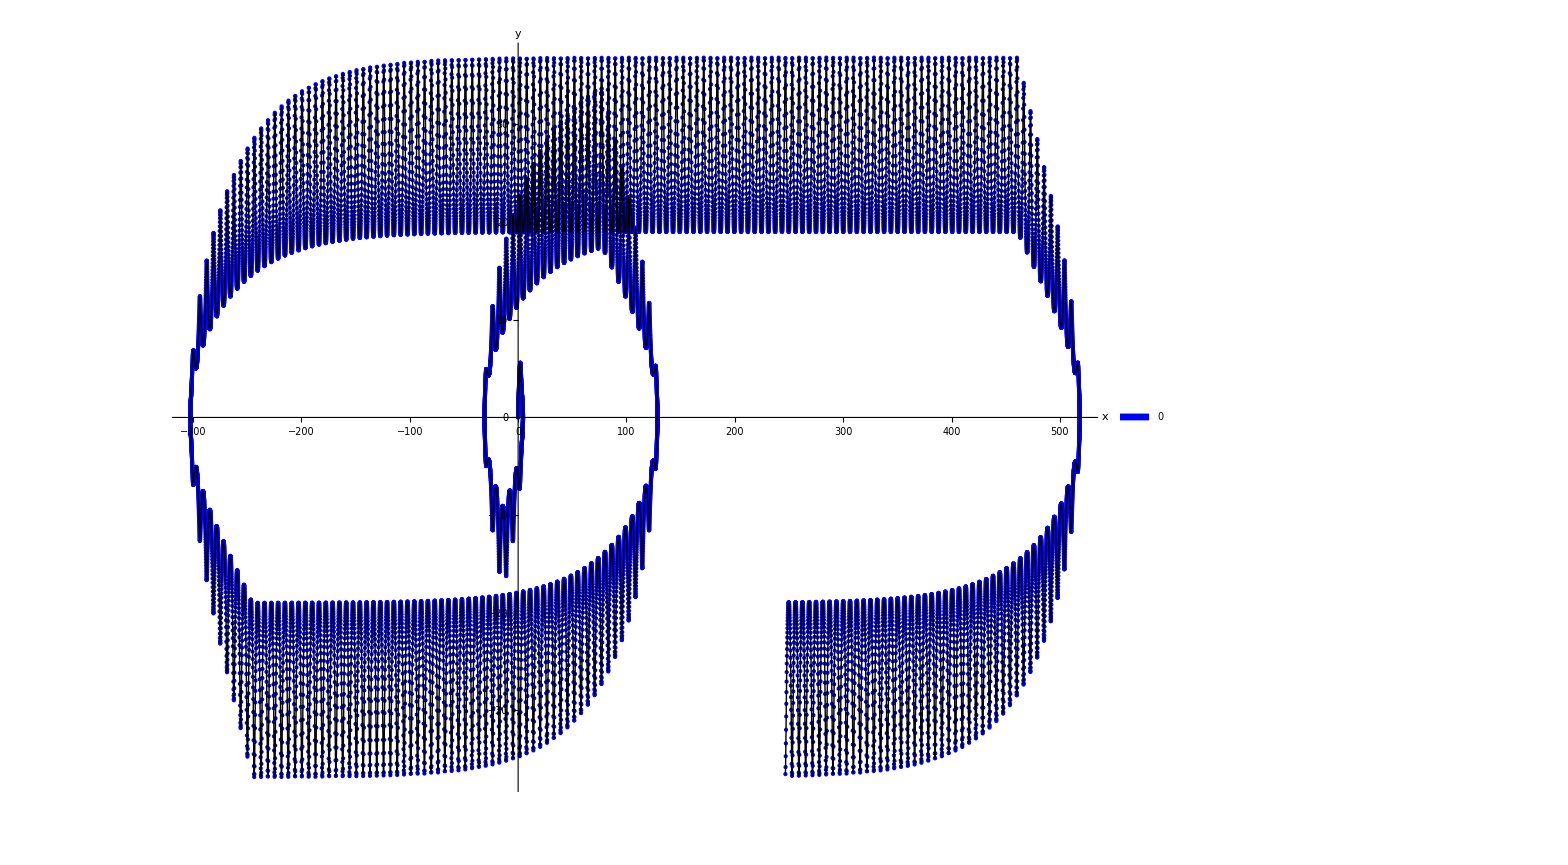

```mathematica
(*ModelLeg, Gravity: 0g, JointVelocity=>x, JointPosition=>y, z => JointTorque, friction 0 0, torque 0.00007, damping 0*)
SetDirectory[NotebookDirectory[]];
chaoticController = Import["log0xf4e9e40PitchChaoticController-vxpyz-0g-force-0-00007-damping-0.tsv","Data"];
jointMovement = Import["log0xf4e9e40PitchJointModel-vxpyz-0g-force-0-00007-damping-0.tsv","Data"];
chaoticControllerTitle= chaoticController[[1,All]];
chaoticController = Drop[chaoticController,1];

jointMovementTitle= jointMovement[[1,All]];
jointMovement = Drop[jointMovement,1][[All,1;;2]];

Show[ListPointPlot3D[{chaoticController}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chaoticControllerTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chaoticController}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}] 

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

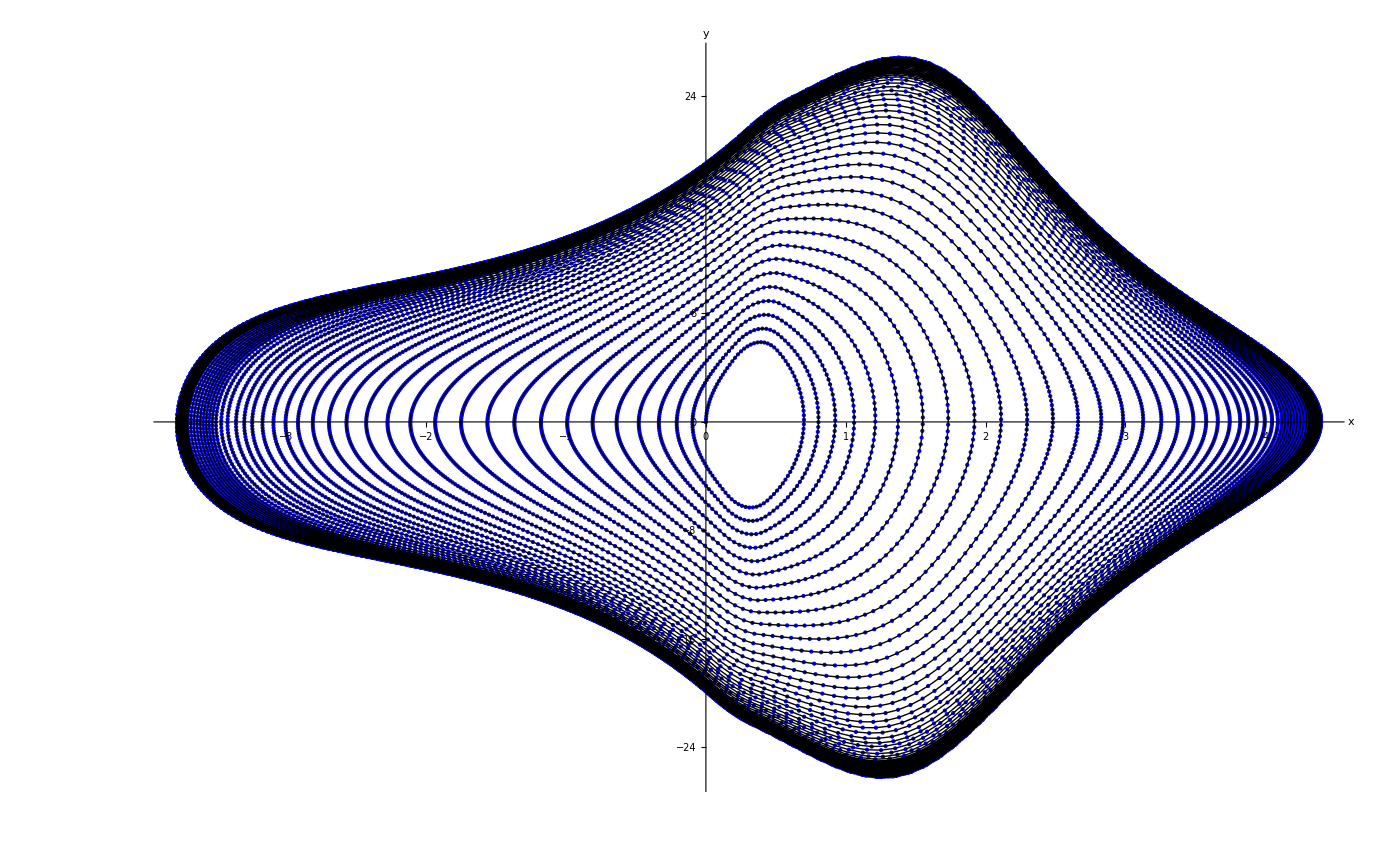

```mathematica
(*ModelLeg,Gravity:0g,JointPosition=>x,JointVelocity=>y,z=>JointTorque,friction 10 10,force 0.7*)
SetDirectory[NotebookDirectory[]];
chuaData0g=Import["ChuaCircuit-modelLeg-0g-100s.tsv","Data"];
chuaTitle0g=chuaData0g[[1,All]];
chuaPlot0g=Drop[chuaData0g,1];
jointMovement = Drop[chuaData0g,1][[All,1;;2]];

Show[ListPointPlot3D[{chuaPlot0g},PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chuaTitle0g,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chuaPlot0g}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

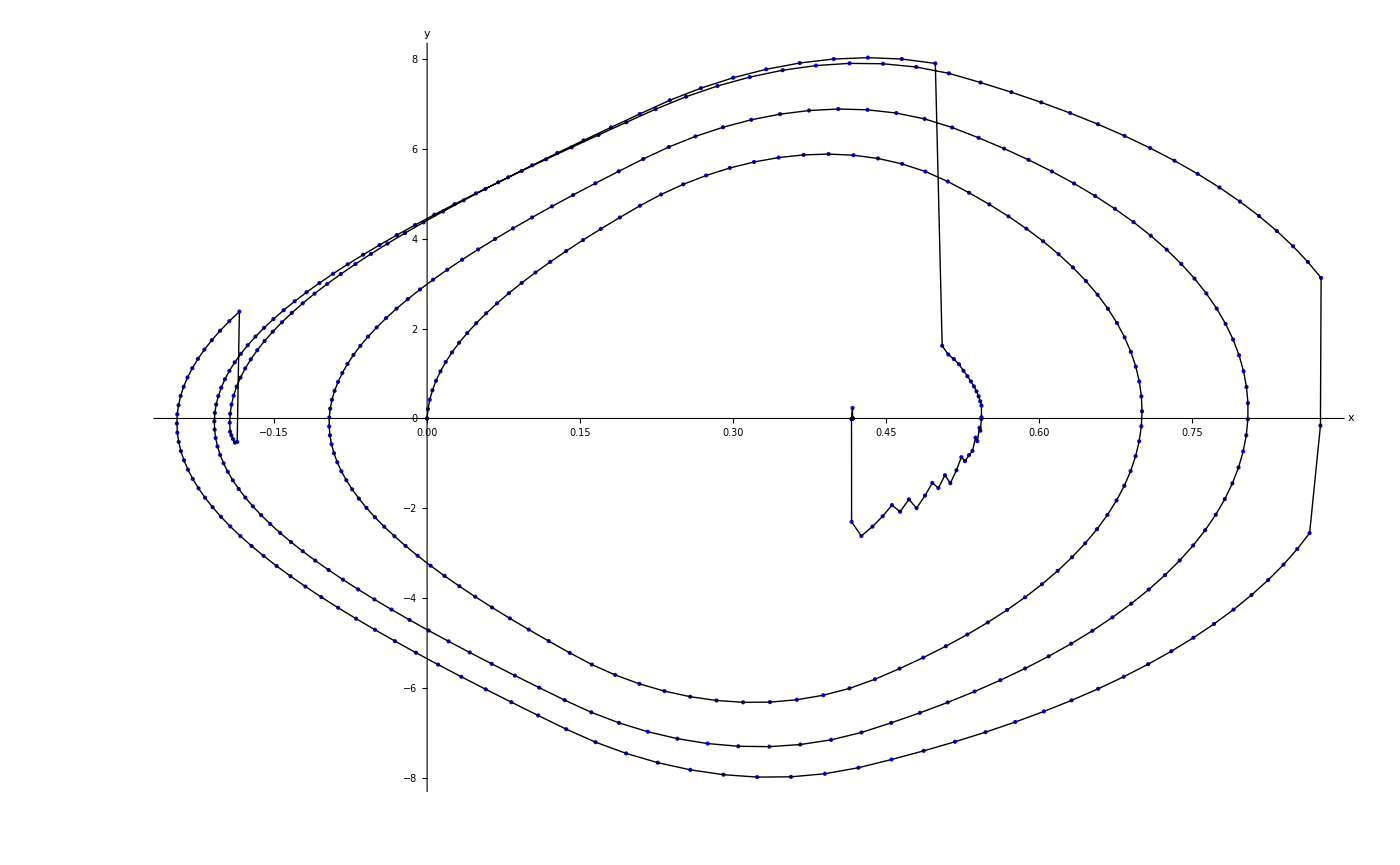

```mathematica
(*ModelLeg, Gravity: 1g, JointPosition => x, JointVelocity => y, z => JointTorque, friction 10 10, force 0.7*)
SetDirectory[NotebookDirectory[]];
chuaData1g = Import["ChuaCircuit-modelLeg-1g-100s.tsv","Data"];
chuaTitle1g = chuaData1g[[1,All]];
chuaPlot1g = Drop[chuaData1g,1];
jointMovement = Drop[chuaData1g,1][[All,1;;2]];

Show[ListPointPlot3D[{chuaPlot1g},PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chuaTitle1g,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chuaPlot1g}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

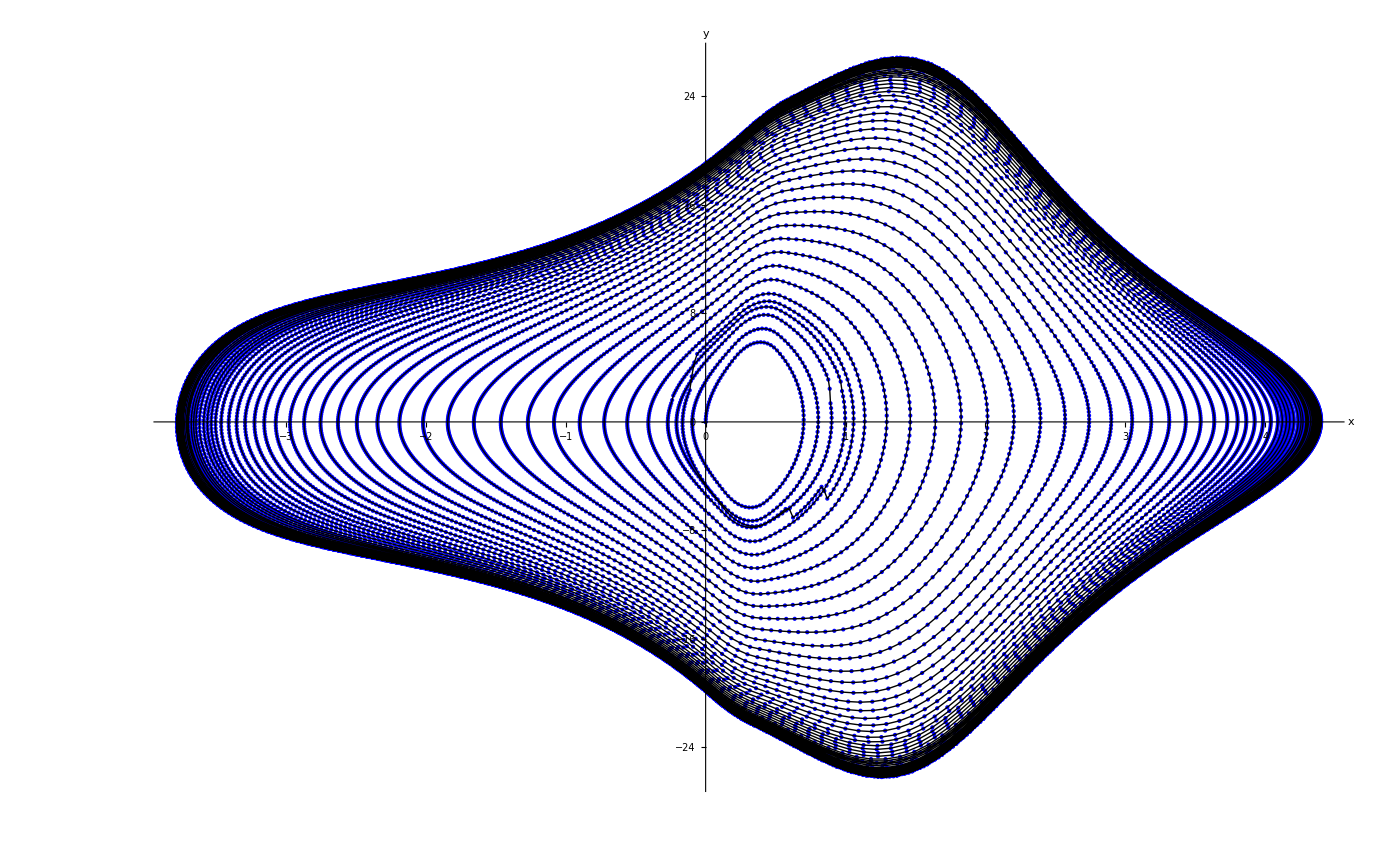

```mathematica
(*ModelLeg, Gravity: 1g, JointPosition => x, JointVelocity => y, z => JointTorque,friction 0 0, force 0.7*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-1g-100s-friction00.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];
jointMovement = Drop[chuaData1g0,1][[All,1;;2]];

Show[ListPointPlot3D[{chuaPlot1g0},PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chuaTitle1g0,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chuaPlot1g0}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

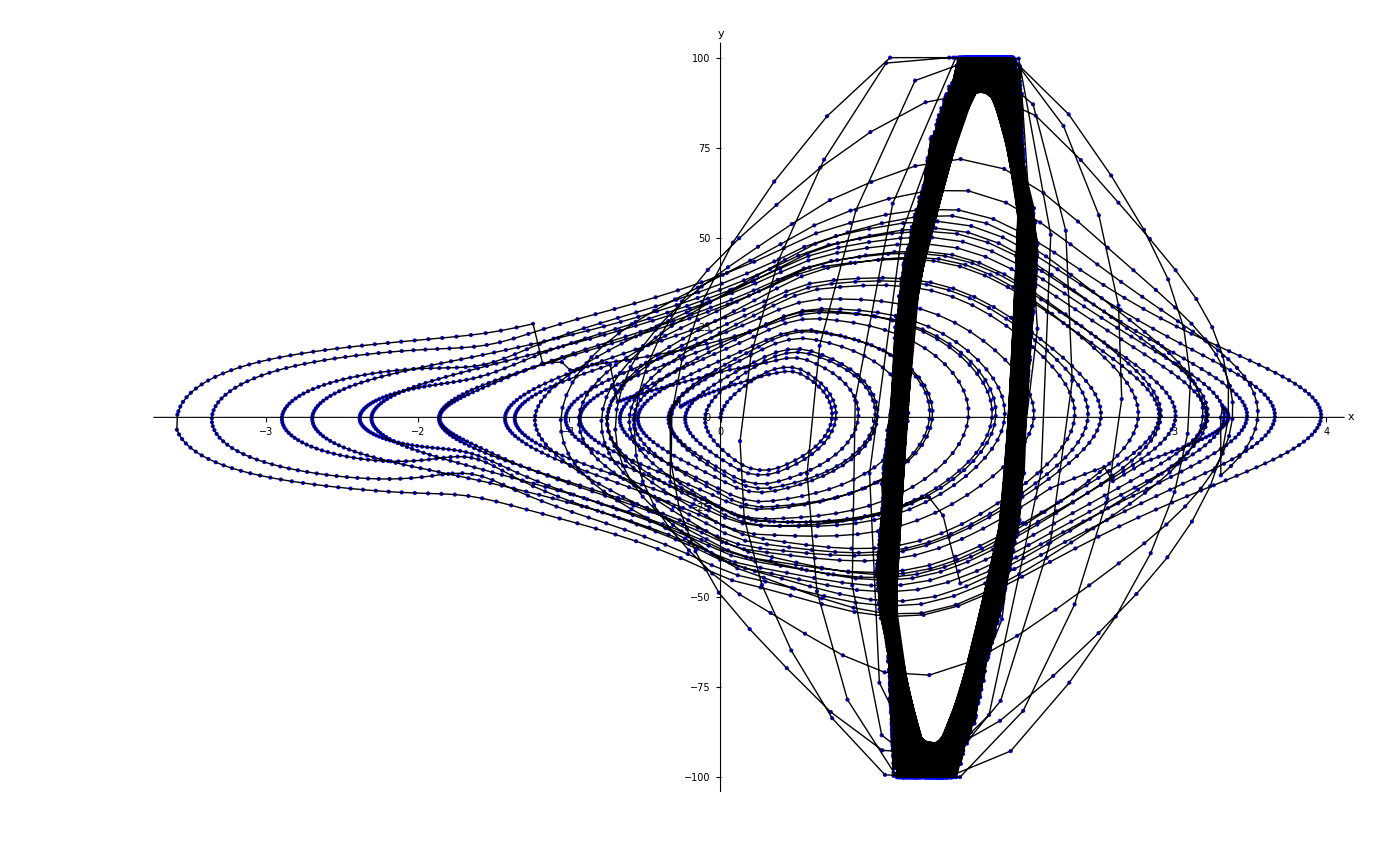

```mathematica
(*ModelLeg, Gravity: 1g, JointPosition => x, JointVelocity => y, z => JointTorque, friction 1 1,force 5*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-1g-100s-friction11-force5.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];
jointMovement = Drop[chuaData1g0,1][[All,1;;2]];

Show[ListPointPlot3D[{chuaPlot1g0},PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chuaTitle1g0,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chuaPlot1g0}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

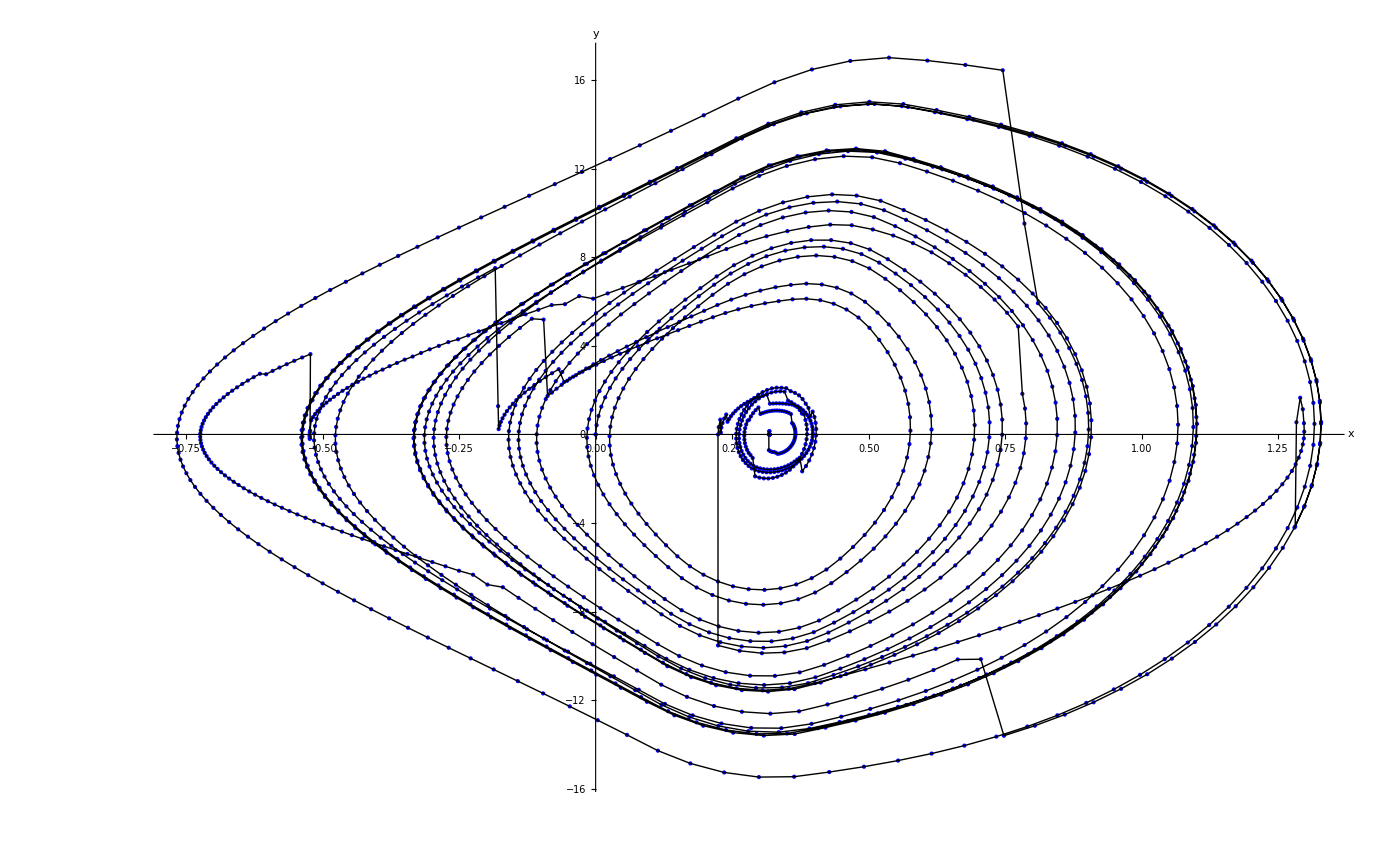

```mathematica
(*ModelLeg, Gravity: 1g,JointPosition => x, JointVelocity => y, z => JointTorque, friction 1 1, force 2*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-1g-100s-friction11-force2.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];
jointMovement = Drop[chuaData1g0,1][[All,1;;2]];

Show[ListPointPlot3D[{chuaPlot1g0},PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chuaTitle1g0,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chuaPlot1g0}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

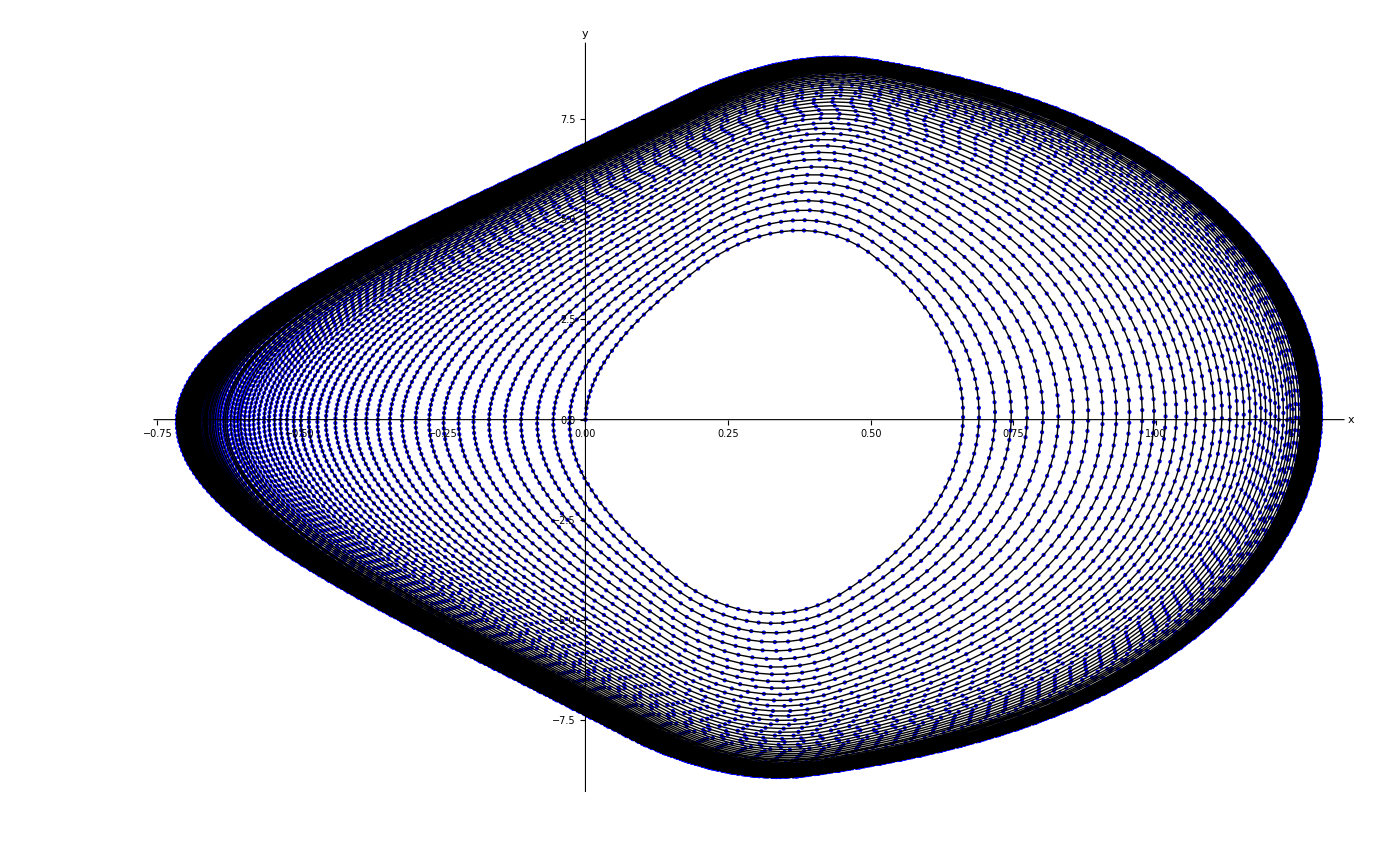

```mathematica
(*ModelLeg, Gravity: 0g, JointPosition => x, JointVelocity => y, z => JointTorque, friction 1 1, force 0.7, damping 0.05*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s-friction11-force07-damping005.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];
jointMovement = Drop[chuaData1g0,1][[All,1;;2]];

Show[ListPointPlot3D[{chuaPlot1g0},PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chuaTitle1g0,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chuaPlot1g0}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

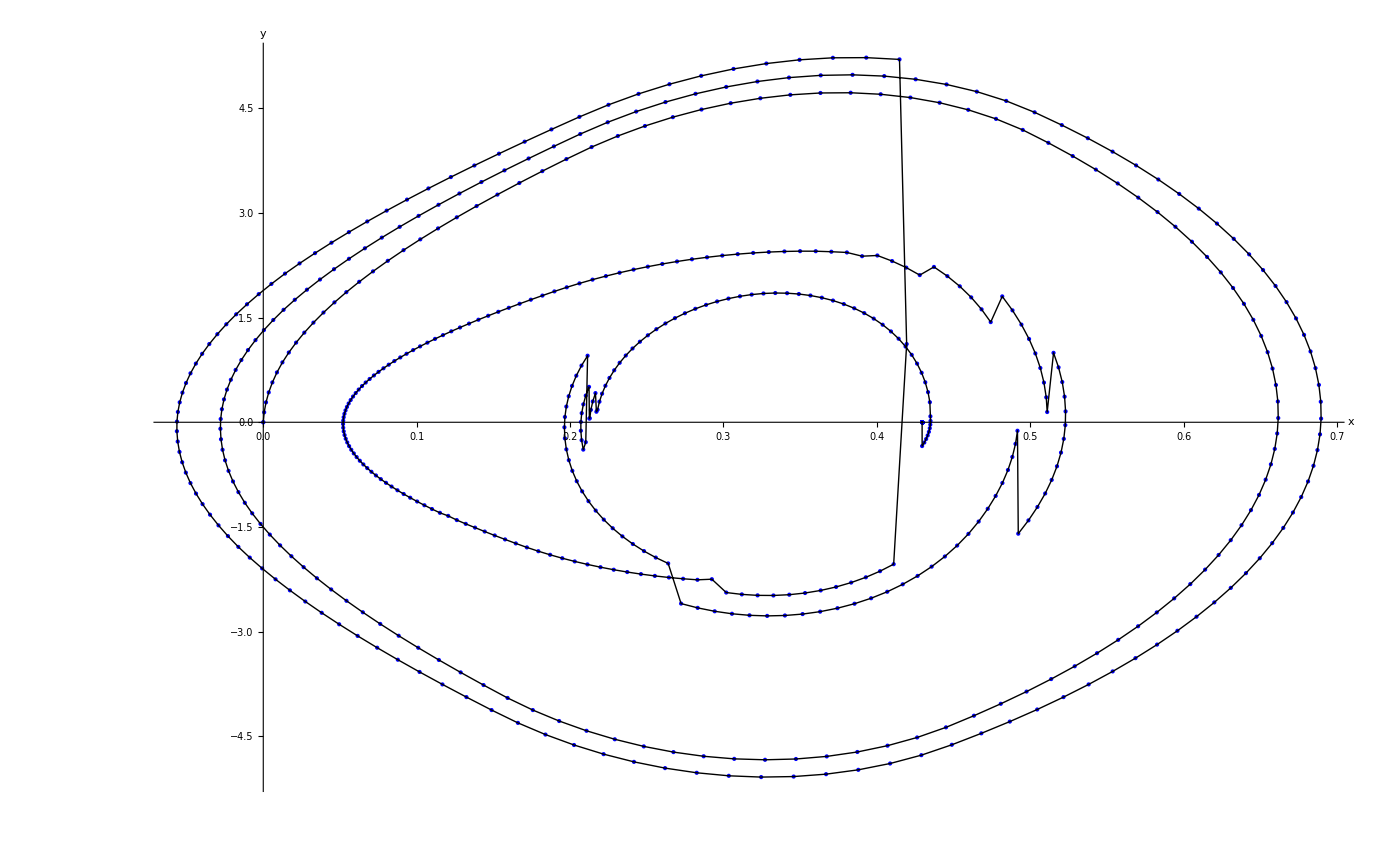

```mathematica
(*ModelLeg, Gravity: 1g, JointPosition => x, JointVelocity => y, z => JointTorque, friction 1 1, force 0.7,damping 0.05*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-1g-100s-friction11-force07-damping005.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];
jointMovement = Drop[chuaData1g0,1][[All,1;;2]];

Show[ListPointPlot3D[{chuaPlot1g0},PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chuaTitle1g0,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chuaPlot1g0}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

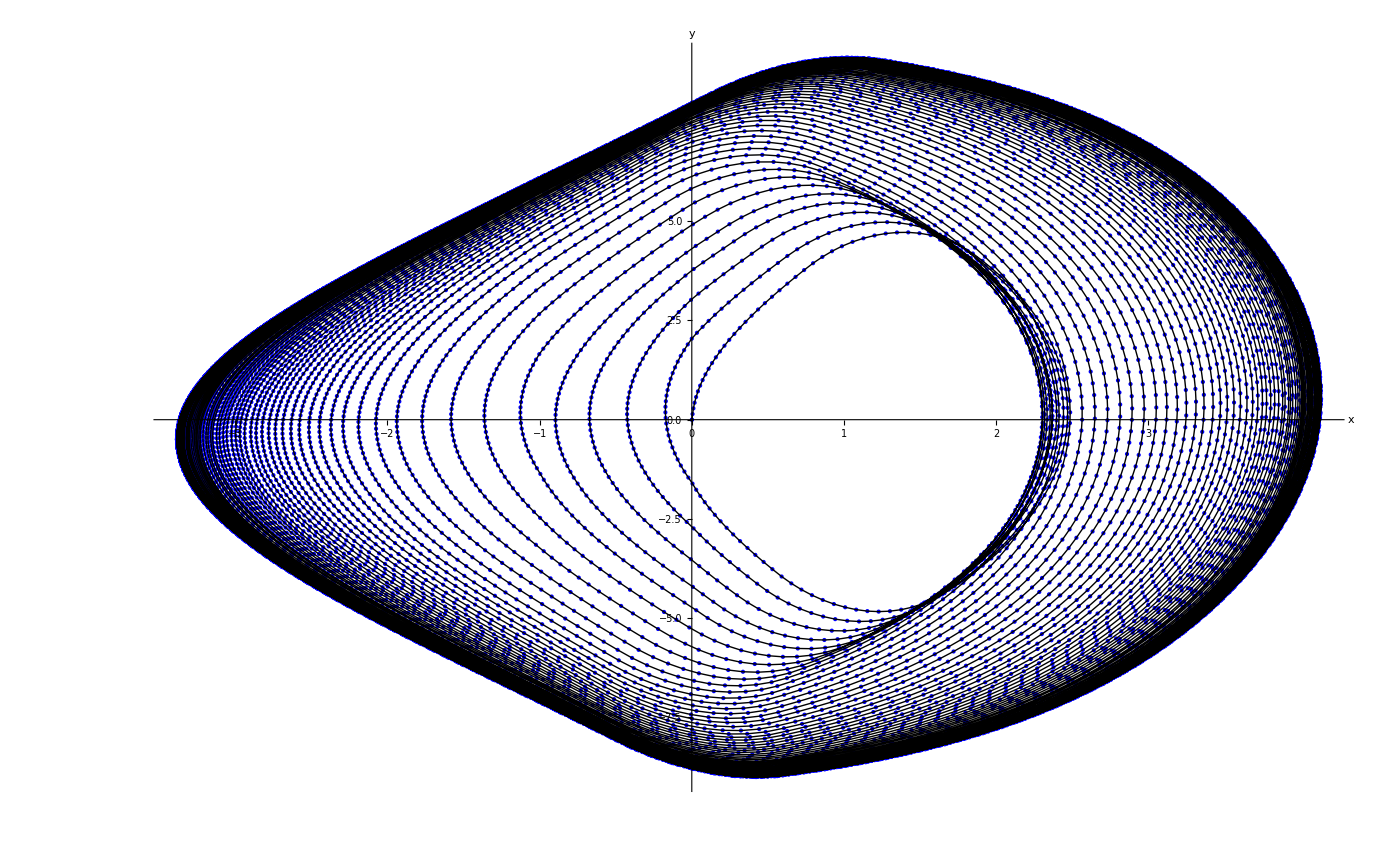

```mathematica
(*ModelLeg, Gravity: 0g, (x), JointVelocity => y, z => JointTorque, friction 1 1,force 0.7, damping 0.05*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s-friction11-force07-(x)yz-damping005.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];
jointMovement = Drop[chuaData1g0,1][[All,1;;2]];

Show[ListPointPlot3D[{chuaPlot1g0},PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chuaTitle1g0,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chuaPlot1g0}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

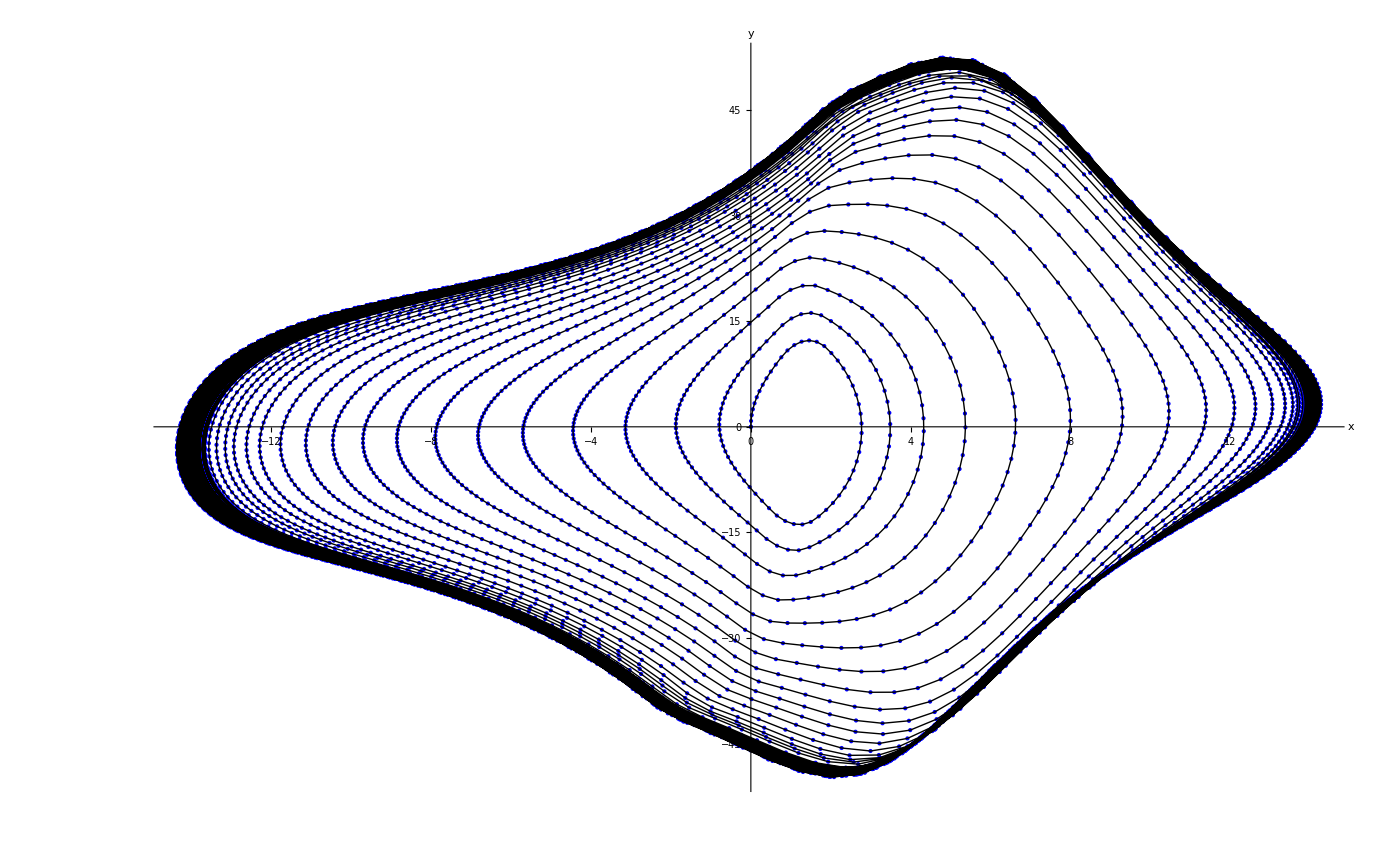

```mathematica
(*ModelLeg, Gravity: 0g, (x), JointVelocity => y, z => JointTorque, friction 1 1,force 4, damping 0.05*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s-friction11-force4-(x)yz-damping005.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];
jointMovement = Drop[chuaData1g0,1][[All,1;;2]];

Show[ListPointPlot3D[{chuaPlot1g0},PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chuaTitle1g0,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chuaPlot1g0}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

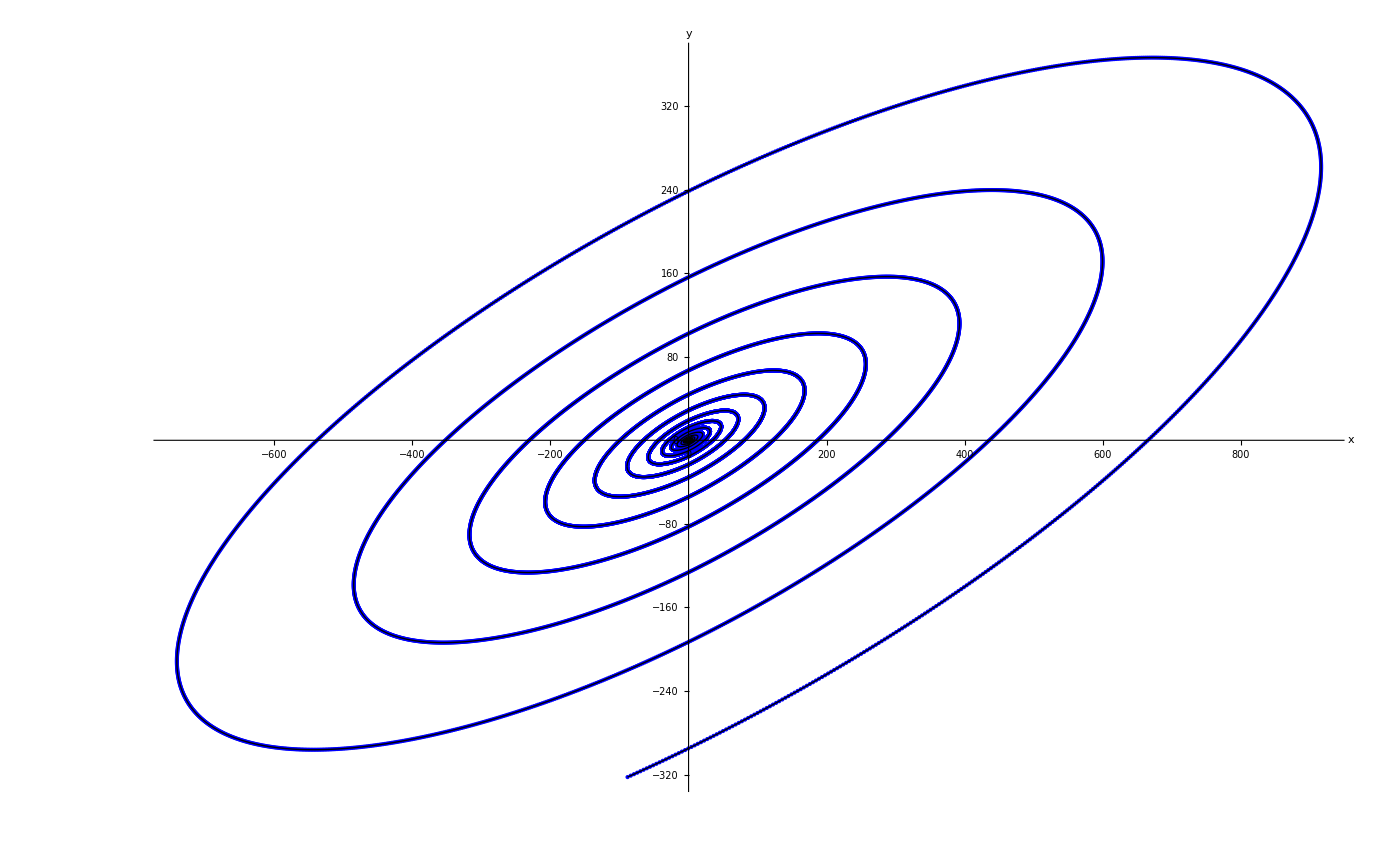

```mathematica
(*ModelLeg, Gravity: 0g, (x),(y), z => JointTorque,friction 0 0, force 0.7, damping 0.05*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s-friction00-force07-(x)(y)z-damping005.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];
jointMovement = Drop[chuaData1g0,1][[All,1;;2]];

Show[ListPointPlot3D[{chuaPlot1g0},PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chuaTitle1g0,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chuaPlot1g0}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

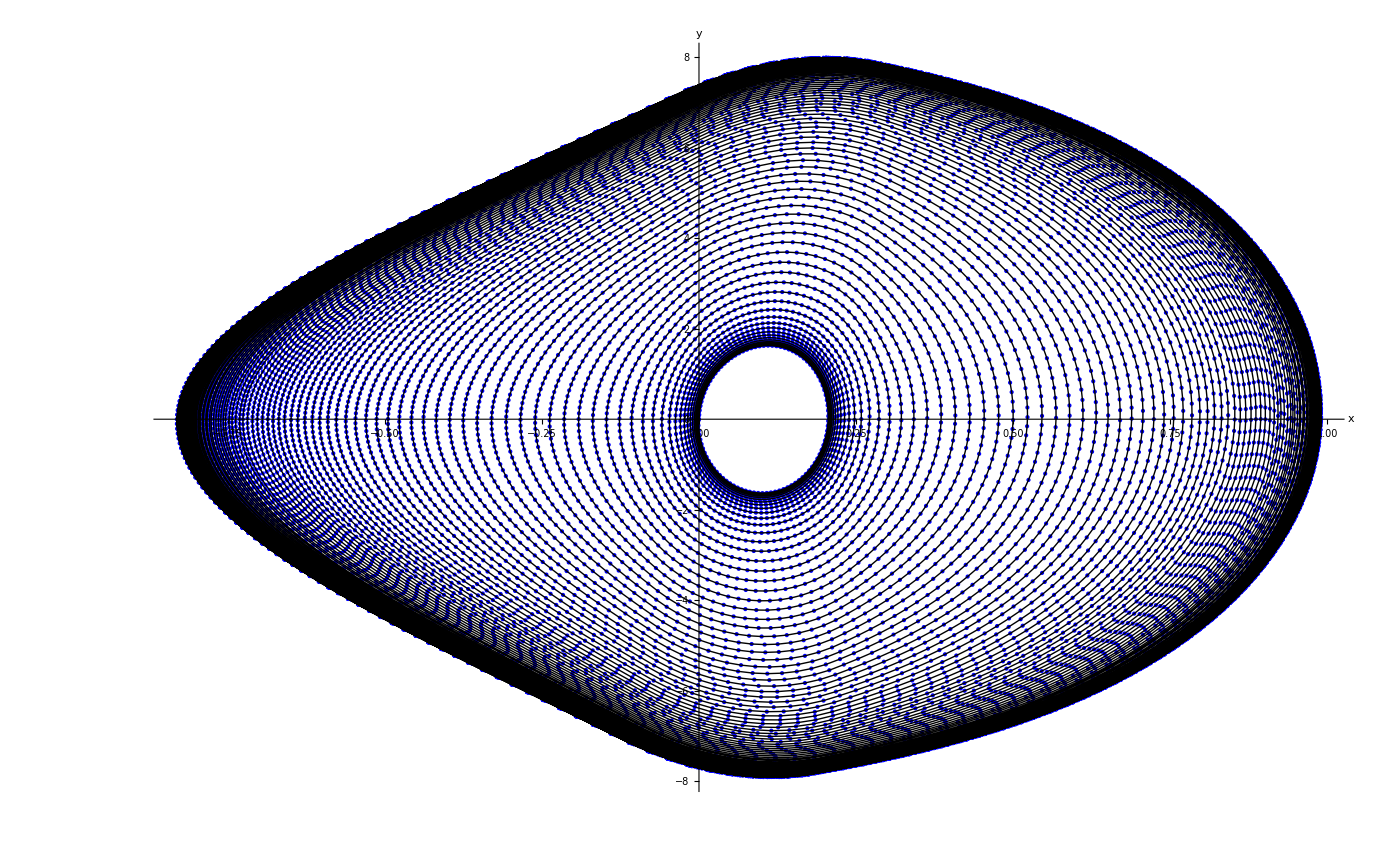

```mathematica
(*ModelLeg, Gravity: 0g, JointPosition => x, JointVelocity => y, z => JointTorque, friction 0 0, force 0.7,damping 0.05*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s-friction00-force07-xyz07-damping005.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];
jointMovement = Drop[chuaData1g0,1][[All,1;;2]];

Show[ListPointPlot3D[{chuaPlot1g0},PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chuaTitle1g0,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chuaPlot1g0}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

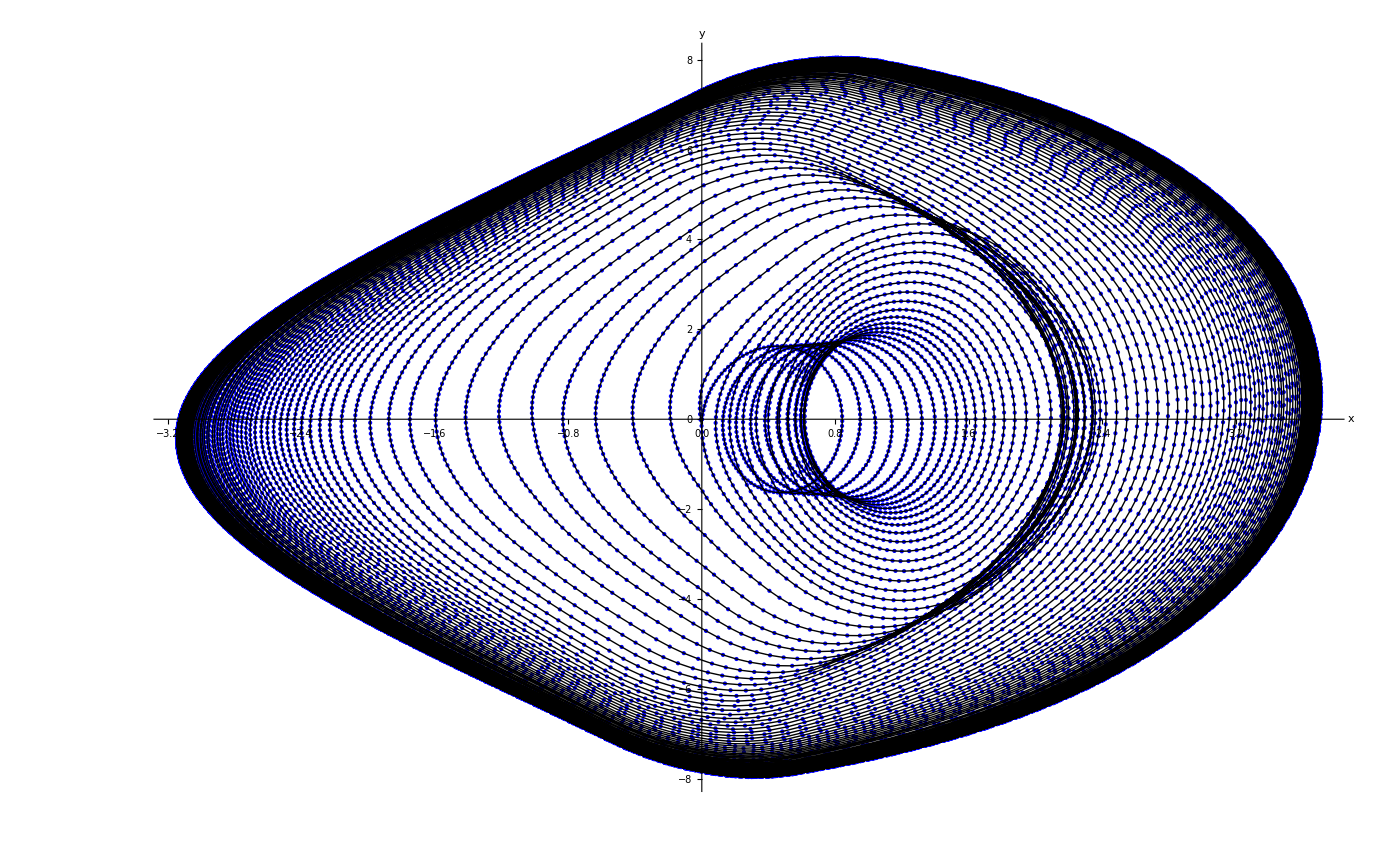

```mathematica
(*ModelLeg, Gravity: 0g, (x), JointVelocity => y, z(0.7) => JointTorque, friction 0 0, force 0.7, damping 0.05*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s-friction00-force07-(x)yz07-damping005.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];
jointMovement = Drop[chuaData1g0,1][[All,1;;2]];

Show[ListPointPlot3D[{chuaPlot1g0},PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chuaTitle1g0,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chuaPlot1g0}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

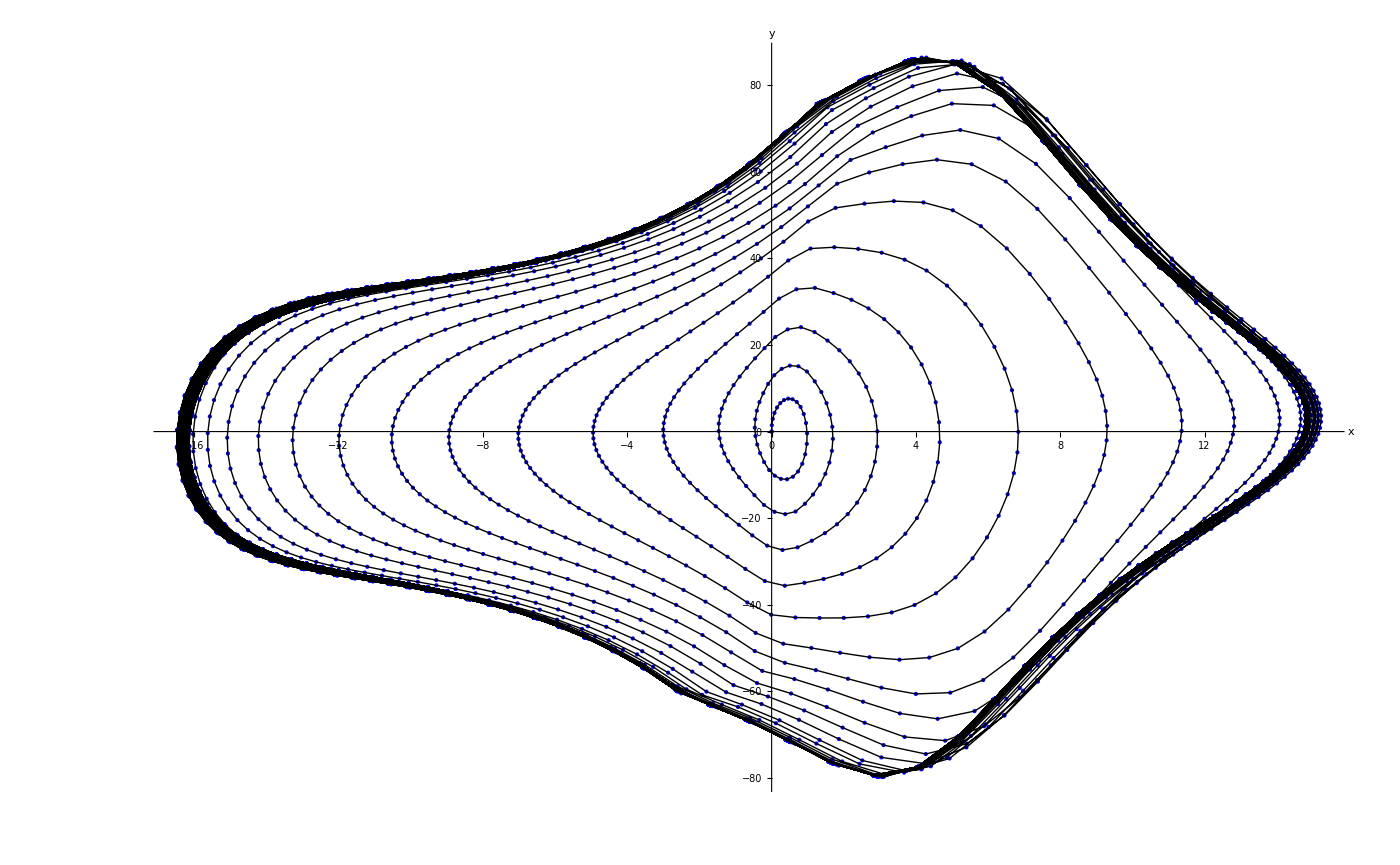

```mathematica
(*ModelLeg, Gravity: 0g, (x), JointVelocity => y, z(0.7) => JointTorque, friction 0 0, force 10, damping 0.05*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s-friction00-force10-(x)yz07-damping005.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];
jointMovement = Drop[chuaData1g0,1][[All,1;;2]];

Show[ListPointPlot3D[{chuaPlot1g0},PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chuaTitle1g0,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chuaPlot1g0}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

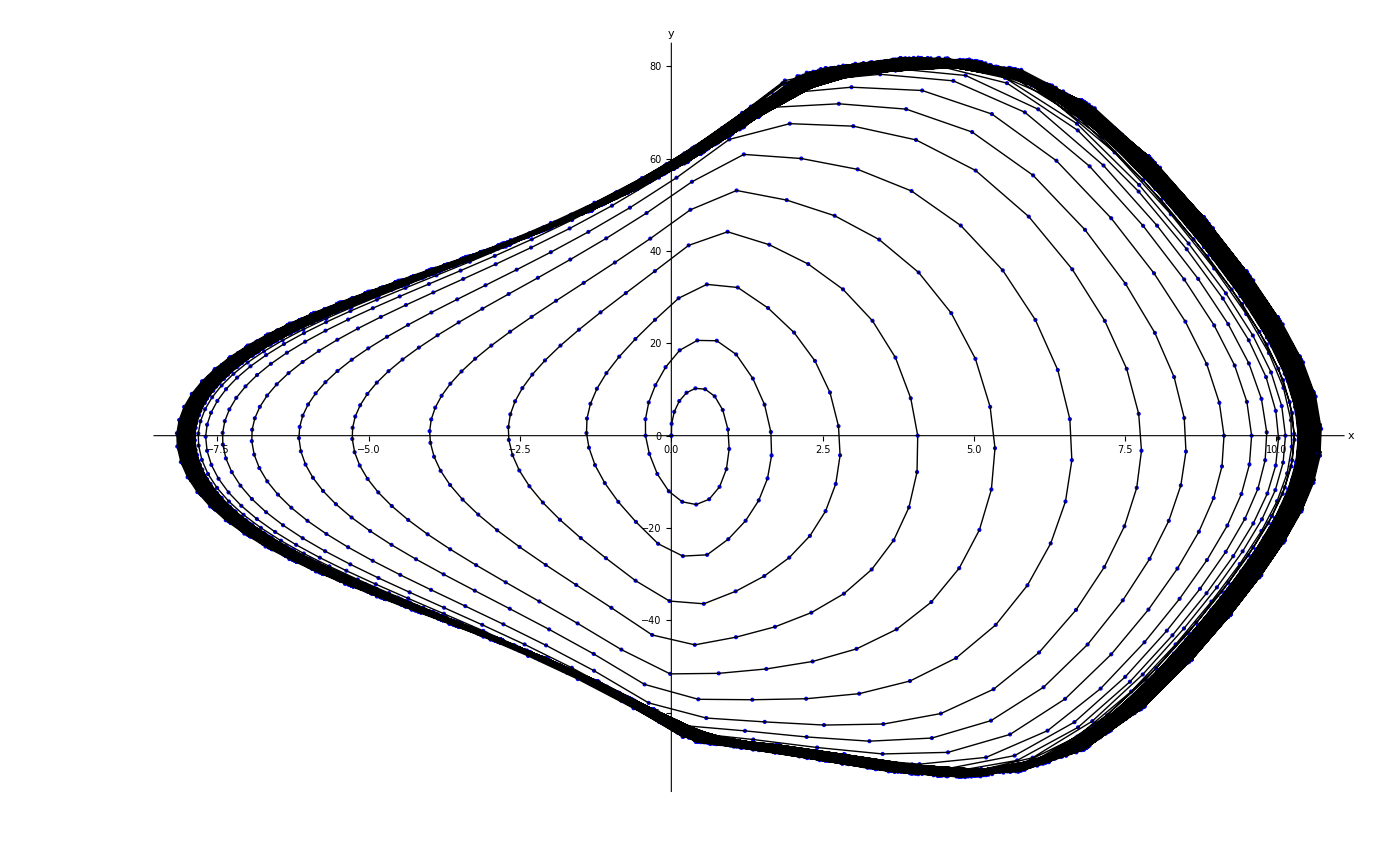

```mathematica
(*ModelLeg, Gravity: 0g, (x), JointVelocity => y, z(0.7) => JointTorque, friction 0 0, force 20, damping 5*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s-friction00-force20-(x)yz07-damping5.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];
jointMovement = Drop[chuaData1g0,1][[All,1;;2]];

Show[ListPointPlot3D[{chuaPlot1g0},PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chuaTitle1g0,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chuaPlot1g0}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

```mathematica
(*ModelLeg, Gravity: 0g, (x), JointVelocity => z, y => JointTorque, friction 0 0, force 0.7,damping 0.5*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s,friction00-force07-(x)(y)z-damping05.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];
jointMovement = Drop[chuaData1g0,1][[All,1;;2]];

Show[ListPointPlot3D[{chuaPlot1g0},PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chuaTitle1g0,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chuaPlot1g0}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

-Graphics-

```mathematica
(*ModelLeg, Gravity: 1g,(x), JointVelocity => y, z => JointTorque,friction 1,1,force 0.7,damping 0.05*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s-friction11-force07-(x)yz-damping005.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];
jointMovement = Drop[chuaData1g0,1][[All,1;;2]];

Show[ListPointPlot3D[{chuaPlot1g0},PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[chuaTitle1g0,LabelStyle->{GrayLevel[0.3],18}]],Graphics3D[Line[{chuaPlot1g0}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue,PlotLegends->SwatchLegend[jointMovementTitle,LabelStyle->{GrayLevel[0.3],18}]],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400]
```

-Graphics3D-

-Graphics-

-Graphics3D-

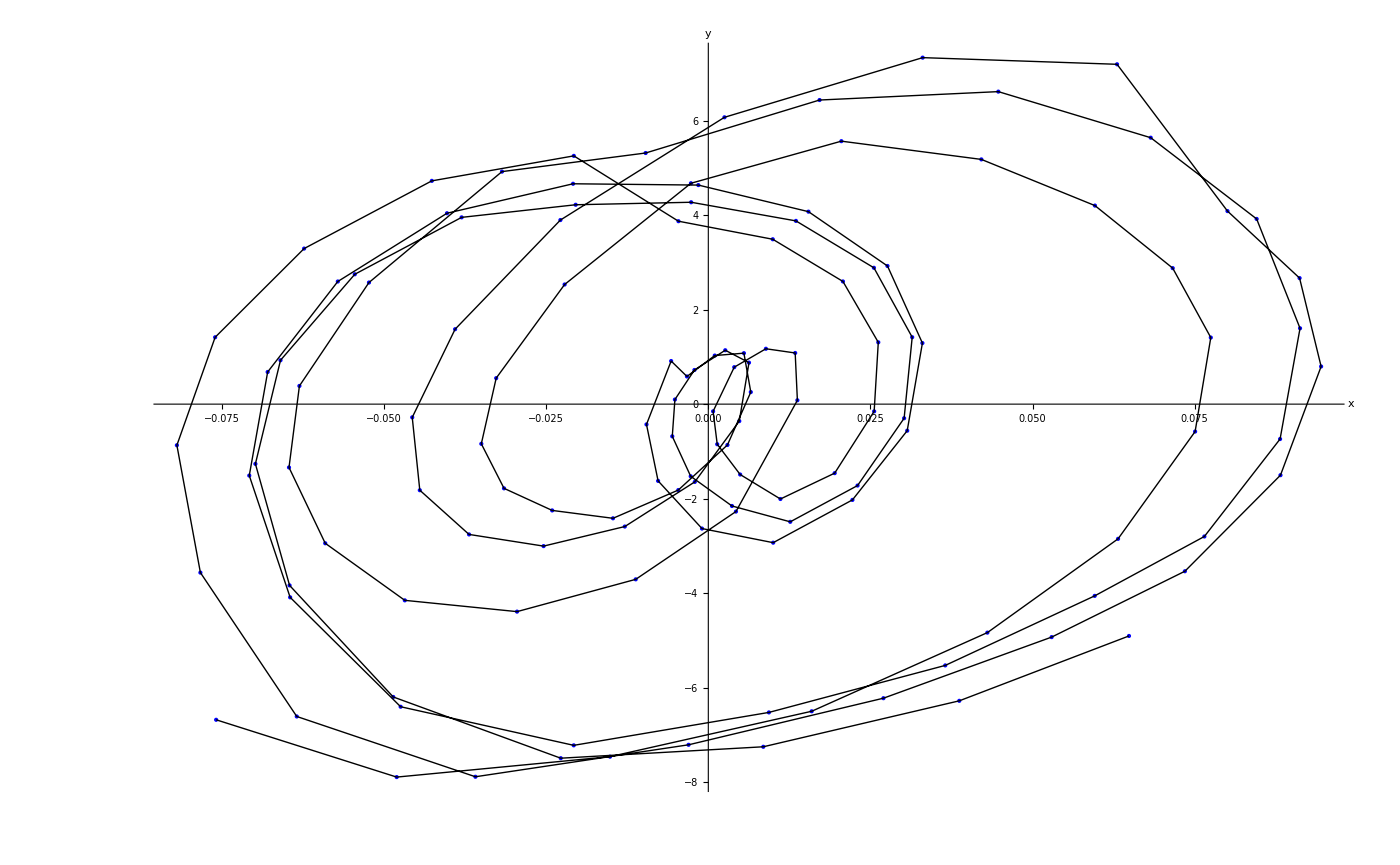

-Graphics-

```mathematica
(*Creature,1g, friction 2 2, force 3*10^-9*mass^2+0.02*mass,xyz,damping [1.0-0.001]*)
SetDirectory[NotebookDirectory[]];
chuaData1 = Import["c1/logChaosLogger0xbbc8700.tsv","Data"]; (*1*)
(*chuaData1 = Import["c1/logChaosLogger0xbbc8840.tsv","Data"];*) (*similar to 1*)
(*chuaData1 = Import["c1/logChaosLogger0xbbc83f0.tsv","Data"];*) (*similar to 1*)
(*chuaData1 = Import["c1/logChaosLogger0xbbc9f50.tsv","Data"];*) (*similar to 1*)
(*chuaData1 = Import["c1/logChaosLogger0xbbca090.tsv","Data"];*) (*similar to 1*)
(*chuaData1 = Import["c1/logChaosLogger0xbbc9d30.tsv","Data"];*) (*similar to 1*)
chuaData2 = Import["c1/logChaosLogger0xbbc6bf0.tsv","Data"]; (*2*)
(*chuaData2 = Import["c1/logChaosLogger0xbbc5060.tsv","Data"]; *)(*similar to 2*)
(*chuaData2 = Import["c1/logChaosLogger0xbbc6d30.tsv","Data"]; *) (*similar to 2*)
(*chuaData2 = Import["c1/logChaosLogger0xbbc51a0.tsv","Data"];*) (*similar to 2*)
(*chuaData2 = Import["c1/logChaosLogger0xbbc4d20.tsv","Data"];*) (*similar to 2*)
(*chuaData2 = Import["c1/logChaosLogger0xbbc68b0.tsv","Data"]; *) (*similar to 2 *)

chuaData3 = Import["c2/logChaosLogger0xbbf2b80.tsv","Data"]; (*3*)
(*chuaData3 = Import["c2/logChaosLogger0xbbf2e90.tsv","Data"]; *) (*similar to 3*)
(*chuaData3 = Import["c2/logChaosLogger0xbbfbce0.tsv","Data"];*) (*simular to 3 Strong limit cycle*)
(*chuaData3 = Import["c2/logChaosLogger0xbbfbee0.tsv","Data"];*) (*simular to 3 Strong limit cycle*)
(*chuaData3 = Import["c2/logChaosLogger0xbbf2fd0.tsv","Data"];*) (*similar to 3*)
chuaData4 = Import["c2/logChaosLogger0xbbf9ee0.tsv","Data"]; (*4*)
(*chuaData3 = Import["c2/logChaosLogger0xbbfc020.tsv","Data"]; *) (*similar to 3*)
(*chuaData4 = Import["c2/logChaosLogger0xbbfa1b0.tsv","Data"]; *) (*simular to 4*)
chuaData5 = Import["c2/logChaosLogger0xbbf81e0.tsv","Data"]; (*5*)
(*chuaData5 = Import["c2/logChaosLogger0xbbf8480.tsv","Data"]; *) (*similar to 5*)
(*chuaData5 = Import["c2/logChaosLogger0xbbef4d0.tsv","Data"]; *) (*similar to 5*)
chuaData6 = Import["c2/logChaosLogger0xbbf6850.tsv","Data"]; (*6*)
(*chuaData4 = Import["c2/logChaosLogger0xbbf4ce0.tsv","Data"]; *) (*simular to 4*)
(*chuaData5 = Import["c2/logChaosLogger0xbbf86d0.tsv","Data"]; *) (*similar to 5*)
(*chuaData5 = Import["c2/logChaosLogger0xbbef190.tsv","Data"]; *) (*similar to 5*)
(*chuaData4 = Import["c2/logChaosLogger0xbbf4ba0.tsv","Data"]; *) (*simular to 4*)
(*chuaData6 = Import["c2/logChaosLogger0xbbf65b0.tsv","Data"]; *) (*similar to 6*)
(*chuaData6 = Import["c2/logChaosLogger0xbbf66f0.tsv","Data"]; *) (*similar to 6*)
(*chuaData4 = Import["c2/logChaosLogger0xbbf4980.tsv","Data"];*) (*similar to 4*)
(*chuaData5 = Import["c2/logChaosLogger0xbbf1340.tsv","Data"]; *) (*similar to 5*)
(*chuaData4 = Import["c2/logChaosLogger0xbbfa2f0.tsv","Data"];*) (*simular to 4*)
(*chuaData5 = Import["c2/logChaosLogger0xbbf1200.tsv","Data"];*) (*similar to 5*)
(*chuaData5 = Import["c2/logChaosLogger0xbbf0ec0.tsv","Data"];*) (*similar to 5*)
(*chuaData5 = Import["c2/logChaosLogger0xbbef610.tsv","Data"]; *) (*similar to 5*)

(*chuaData3 = Import["c3/logChaosLogger0xbbdf750.tsv","Data"]; *) (*similar to 3*)
chuaData7 = Import["c3/logChaosLogger0xbbd89a0.tsv","Data"];  (*7 highly chaotic behavior*)
(*chuaData7 = Import["c3/logChaosLogger0xbbd6c90.tsv","Data"]; *) (* similar to 7*)
(*chuaData3 = Import["c3/logChaosLogger0xbbdbe10.tsv","Data"];*) (*similar to 3*)
(*chuaData3 = Import["c3/logChaosLogger0xbbdfac0.tsv","Data"];*) (*similar to 3*)
(*chuaData7 = Import["c3/logChaosLogger0xbbd8c20.tsv","Data"];*) (* similar to 7*)
chuaData8 = Import["c3/logChaosLogger0xbbd3440.tsv","Data"]; (*8*)
(*chuaData3 = Import["c3/logChaosLogger0xbbdda30.tsv","Data"];*) (*similar to 3*)
(*chuaData7 = Import["c3/logChaosLogger0xbbd70a0.tsv","Data"]; *) (* similar to 7*)
(*chuaData3 = Import["c3/logChaosLogger0xbbdc300.tsv","Data"];*) (*similar to 3*)
(*chuaData8 = Import["c3/logChaosLogger0xbbd3890.tsv","Data"]; *) (*similar to 8*)
(*chuaData3 = Import["c3/logChaosLogger0xbbdde40.tsv","Data"];*) (* similar to 3*)
(*chuaData7 = Import["c3/logChaosLogger0xbbd5070.tsv","Data"];*) (* similar to 7*)
(*chuaData7 = Import["c3/logChaosLogger0xbbd8ae0.tsv","Data"];*) (* similar to 7*)
(*chuaData8 = Import["c3/logChaosLogger0xbbda7f0.tsv","Data"];*) (*similar to 8*)
(*chuaData7 = Import["c3/logChaosLogger0xbbd6f60.tsv","Data"];*) (* similar to 7*)
(*chuaData7 = Import["c3/logChaosLogger0xbbd5410.tsv","Data"];*) (* similar to 7*)
(*chuaData7 = Import["c3/logChaosLogger0xbbdf980.tsv","Data"];*) (*similar to 3*)
(*chuaData3 = Import["c3/logChaosLogger0xbbdc0b0.tsv","Data"];*) (*similar to 3*)
(*chuaData8 = Import["c3/logChaosLogger0xbbd3750.tsv","Data"];*) (*similar to 8*)
(*chuaData3 = Import["c3/logChaosLogger0xbbddd00.tsv","Data"];*) (*similar to 3*)
(*chuaData7 = Import["c3/logChaosLogger0xbbd52d0.tsv","Data"];*) (* similar to 7*)
(*chuaData8 = Import["c3/logChaosLogger0xbbda530.tsv","Data"];*) (*similar to 8*)
(*chuaData8 = Import["c3/logChaosLogger0xbbda670.tsv","Data"];*) (*similar to 8*)

chuaTitle1 = chuaData1[[1,All]];
chuaPlot1 = Drop[chuaData1,1];
jointMovement = Drop[chuaPlot1,1][[All,1;;2]];
cp1 = Show[ListPointPlot3D[{chuaPlot1},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1}],AspectRatio->1,PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400(*,PlotLabel->chuaTitle1*)];
c1 = Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400];

chuaTitle2 = chuaData2[[1,All]];
chuaPlot2 = Drop[chuaData2,1];
jointMovement = Drop[chuaPlot2,1][[All,1;;2]];
cp2 = Show[ListPointPlot3D[{chuaPlot2},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot2}],AspectRatio->1,PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400(*,PlotLabel->chuaTitle2*)];
c2 = Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400] ;

chuaTitle3 = chuaData3[[1,All]];
chuaPlot3 = Drop[chuaData3,1];
jointMovement = Drop[chuaPlot3,1][[All,1;;2]];
cp3 = Show[ListPointPlot3D[{chuaPlot3},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot3}],AspectRatio->1,PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400(*,PlotLabel->chuaTitle3*)];
c3 = Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400];

chuaTitle4 = chuaData4[[1,All]];
chuaPlot4 = Drop[chuaData4,1];
jointMovement = Drop[chuaPlot3,1][[All,1;;2]];
(*jointMovement = Drop[Drop[chuaPlot4,1][[All,1;;2]],1900];*)
cp4 = Show[ListPointPlot3D[{chuaPlot4},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot4}],AspectRatio->1,PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400(*,PlotLabel->chuaTitle4*)];
c4 = Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400] ;

chuaTitle5 = chuaData5[[1,All]];
chuaPlot5 = Drop[chuaData5,1];
jointMovement = Drop[chuaPlot5,1][[All,1;;2]];
cp5 = Show[ListPointPlot3D[{chuaPlot5},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot5}],AspectRatio->1,PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400(*,PlotLabel->chuaTitle5*)];
c5 = Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400] ;

chuaTitle6 = chuaData6[[1,All]];
chuaPlot6 = Drop[chuaData6,1];
jointMovement = Drop[chuaPlot6,1][[All,1;;2]];
cp6 = Show[ListPointPlot3D[{chuaPlot6},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot6}],AspectRatio->1,PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400(*,PlotLabel->chuaTitle6*)];
c6 = Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400] ;

chuaTitle7 = chuaData7[[1,All]];
chuaPlot7 = Drop[chuaData7,1];
jointMovement = Drop[chuaPlot7,1][[All,1;;2]];
cp7 = Show[ListPointPlot3D[{chuaPlot7},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot7}],AspectRatio->1,PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400(*,PlotLabel->chuaTitle7*)];
c7 = Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400] ;

chuaTitle8 = chuaData8[[1,All]];
chuaPlot8 = Drop[chuaData8,1];
jointMovement = Drop[chuaPlot8,1][[All,1;;2]];
cp8 = Show[ListPointPlot3D[{chuaPlot8},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot8}],AspectRatio->1,PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400(*,PlotLabel->chuaTitle8*)];
c8 = Show[ListPlot[{jointMovement}, PlotRange->All,PlotStyle->Blue],Graphics[Line[{jointMovement}],PlotRange->All],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400] ;
GraphicsGrid[{{cp1,c1},{cp2,c2},{cp3,c3},{cp4,c4},{cp5,c5},{cp6,c6},{cp7,c7},{cp8,c8}}]
```

```mathematica
|
```

```mathematica
Set current working directory to Notebook directory
SetDirectory["/home/leviathan/git/minemonics/Minemonics/doc/reports/Thesis/Pictures/model-organisms/model-leg"];
```

current directory^2 Notebook Set to working

```mathematica
current directory^2 Notebook Set to working
```

current directory^2 Notebook Set to working

```mathematica
NotebookDirectory[]
```

/home/leviathan/meta/Work.Repositories/git/minemonics/Minemonics/doc/measurements/